```mathematica
AppendTo[$Path,"~/projects/KnotTheory/trunk/"];
```

```mathematica
<<KnotTheory`
```

Loading KnotTheory` version of February 5, 2013, 3:48:46.4762.
Read more at http://katlas.org/wiki/KnotTheory.

KnotTheory::loading: Loading precomputed data in "PD4Knots`".

KnotTheory::credits: "DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004."

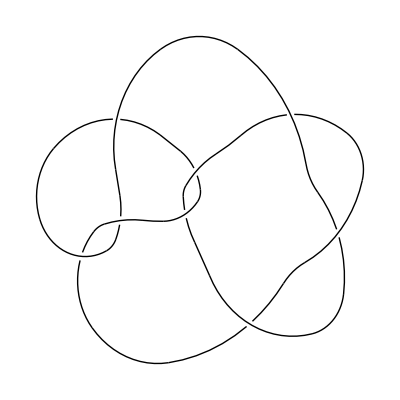

```mathematica
DrawPD[Knot[8,19]]
```

```mathematica
Writhe[k:(_Knot|_Link|_BR)]:=Writhe[PD[k]]
Writhe[p_PD]:=With[{o=OPD[p]},Count[o,_Xp]-Count[o,_Xn]]
```

```mathematica
RotateBox[X_,0]:=X
RotateBox[RotateBox[X_,k_],l_]:=RotateBox[X,k+l]
```

```mathematica
ClearAll[PlanarDiagram]
```

```mathematica
SetAttributes[PlanarDiagram,{Flat,Orderless,OneIdentity}]
```

```mathematica
PlanarDiagram[Box[{a_,a_,b___},X_]]:=PlanarDiagram[Box[{b},Stitch[X]]]
PlanarDiagram[Box[{a__,b_,b_,c___},X_]]:=PlanarDiagram[Box[{b,b,c,a},RotateBox[X,Length[{a}]]]]
```

```mathematica
PlanarDiagram[Box[{a_,b_,c_,d_},X_],Box[{d_,c_,e___},Y_]]:=PlanarDiagram[Box[{a,b,e},Multiply[2][X,Y]]]
PlanarDiagram[Box[{a___,b_,c_,d___},X_],Box[{e___,c_,b_,f___},Y_]]:=PlanarDiagram[Box[{d,a,b,c},RotateBox[X,-Length[{d}]]],Box[{c,b,f,e},RotateBox[Y,Length[{e}]]]]
PlanarDiagram[Box[{a_,b___,c_},X_],Box[{d___,a_,c_,e___},Y_]]:=PlanarDiagram[Box[{b,c,a},RotateBox[X,1]],Box[{a,c,e,d},RotateBox[Y,Length[{d}]]]]
PlanarDiagram[Box[{a___,b_,c_,d__},X_],Box[{b_,e___,c_},Y_]]:=PlanarDiagram[Box[{d,a,b,c},RotateBox[X,-Length[{d}]]],Box[{c,b,e},RotateBox[Y,-1]]]
PlanarDiagram[Box[{a_,b___,c_},X_],Box[{c_,d___,a_},Y_]]:=PlanarDiagram[Box[{b,c,a},RotateBox[X,1]],Box[{a,c,d},RotateBox[Y,-1]]]
```

```mathematica
PlanarDiagram[Box[{a___,b_,c___},X_],Box[{d___,b_,e___},Y_]]:=PlanarDiagram[Box[{c,a,e,d},Multiply[1][RotateBox[X,-Length[{c}]],RotateBox[Y,Length[{d}]]]]]
```

```mathematica
PlanarDiagram[p_OPD]:=PlanarDiagram@@(p/.{Xp[a_,b_,c_,d_]:>Box[{c,d,a,b},Xp],Xn[a_,b_,c_,d_]:>Box[{b,c,d,a},Xn]})
```

```mathematica
PlanarDiagram[unlink=OPD[Xn[1,3,2,4],Xp[2,3,1,4]]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][Xn,Xp],1]]]]]

```mathematica
OPD[PD[crossings___]]:=OPD[crossings]/.{X[i_,j_,k_,l_]/;(j-l==1||l-j>1):>Xp[i,j,k,l],X[i_,j_,k_,l_]/;(l-j==1||j-l>1):>Xn[i,j,k,l]}
OPD[K_Knot]:=OPD[PD[K]]
OPD[L_Link]:=OPD[PD[L]]
```

```mathematica
PlanarDiagram[K:(_Knot|_Link)]:=Module[{result},
result=Quiet[PlanarDiagram[OPD[K]],$IterationLimit::itlim];
If[FreeQ[result,Hold],
PlanarDiagram[K]=result,
$Failed]
]
```

```mathematica
PlanarDiagram[Knot[8,19]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][Xp,Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-2],RotateBox[Xp,1]],-1]],1]]],1]]]]]

```mathematica
(PlanarDiagram/@AllKnots[8])⟦All,1,1⟧
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Cases[AllKnots[{3,11}],K_/;PlanarDiagram[K]⟦1,1⟧≠{}]
```

{}

```mathematica
Cases[AllKnots[12],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

{Knot[12,Alternating,1251]}

```mathematica
Cases[AllKnots[13],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

$Aborted

```mathematica
Cases[AllKnots[14],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

```mathematica
Cases[AllKnots[15],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

```mathematica
Cases[AllKnots[16],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

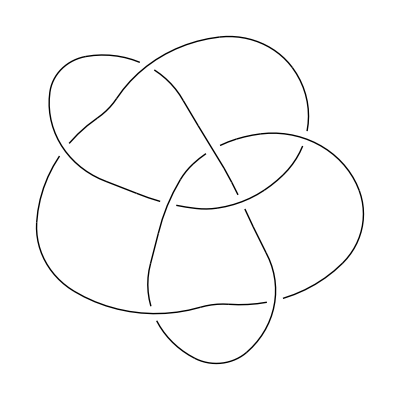

```mathematica
DrawPD[Knot[8,16]]
```

```mathematica
PlanarDiagram[Knot[8,16]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xn,-1],RotateBox[Xn,-1]],-2],RotateBox[Multiply[2][Multiply[2][RotateBox[Xn,-1],RotateBox[Xn,-1]],RotateBox[Multiply[2][RotateBox[Xn,-2],RotateBox[Multiply[1][RotateBox[Xp,-1],RotateBox[Xp,3]],2]],1]],4]],1]],2],RotateBox[Xp,-1]],1]]]]]

### Loading matrices

```mathematica
Clear[QESRotation,QESBraiding,QESInverseBraiding,QESCupCap,QESCap,QESCup,QESI,QESH,QESFork,QESFuse]
```

```mathematica
ZeroMatrix[n_]:=Table[0,{n},{n}]
ZeroMatrix[n_,m_]:=Table[0,{n},{m}]
```

```mathematica
QESDimension[n_]:=Length[QESRotation[n]]
```

```mathematica
QESId[n_]:=IdentityMatrix[QESDimension[n]]
QESZero[n_,m_]:=ZeroMatrix[QESDimension[n],QESDimension[m]]
QESRotation[0]:={{1}}
QESRotation[1]:={}
QESRotation[n_]:=QESRotation[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-rotation-matrix.m"}]];
QESRotation[n_,k_]/;k<0∨k≥n:=QESRotation[n,Mod[k,n]]
QESRotation[n_,0]:=IdentityMatrix[Length[QESRotation[n]]]
QESRotation[n_,1]:=QESRotation[n]
QESRotation[n_,k_]:=QESRotation[n,k]=Together[QESRotation[n].QESRotation[n,k-1]]
QESBraiding[n_]:=QESBraiding[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-braiding-matrix.m"}]];
QESBraiding[n_,k_]:=QESBraiding[n,k]=Together[QESRotation[n,-k].QESBraiding[n].QESRotation[n,k]]
QESInverseBraiding[n_]:=QESInverseBraiding[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-inverse-braiding-matrix.m"}]];
QESCupCap[n_]:=QESCupCap[n]=Together[QESCup[n-2].QESCap[n]]
QESCupCap[3]={{0}};
QESCup[0]={{1}};
QESCup[1]={{}};
QESCup[n_]:=QESCup[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-cup-matrix.m"}]]
QESCap[2]={{d}};
QESCap[n_]:=QESCap[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-cap-matrix.m"}]]
QESI[n_]:=QESI[n]=Together[QESFork[n-1].QESFuse[n]]
QESFork[n_]:=QESFork[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-fork-matrix.m"}]]
QESFuse[n_]:=QESFuse[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-fuse-matrix.m"}]]
QESH[n_]:=QESH[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-H-matrix.m"}]]
```

### Verifying matrices

```mathematica
Table[Together[QESRotation[k,k-1].QESRotation[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESCupCap[k].QESCupCap[k]==d QESCupCap[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESFuse[k+2].QESCup[k]==QESZero[k+1,k],{k,1,4}]
```

{True,True,True,True}

```mathematica
Table[Together[QESBraiding[k].QESInverseBraiding[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[Together[QESInverseBraiding[k].QESBraiding[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESBraiding[k+1].QESFork[k]==(-v^6)QESFork[k],{k,2,5}]
```

{True,True,True,True}

```mathematica
Table[QESInverseBraiding[k+1].QESFork[k]==(-v^-6)QESFork[k],{k,2,5}]
```

{True,True,True,True}

```mathematica
Table[QESBraiding[k+2].QESCup[k]==(v^12)QESCup[k],{k,2,4}]
```

{True,True,True}

```mathematica
Table[QESInverseBraiding[k+2].QESCup[k]==(v^-12)QESCup[k],{k,2,4}]
```

{True,True,True}

```mathematica
Table[Together[QESBraiding[k,0].QESBraiding[k,1].QESBraiding[k,0]-QESBraiding[k,1].QESBraiding[k,0].QESBraiding[k,1]]==QESZero[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
(* There's still lots more interesting stuff that could be verified here. *)
```

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESCupCap[k],{k,2,6}]]]
```

v^18 (1+v^4) (1+v^2+v^4) (1+d v^2+v^4) (1+d v^8+v^16)^2

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESI[k],{k,3,6}]]]
```

v^18 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4)^2 (1+d v^2+v^4) (1+d v^8+v^16)^3

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESH[k],{k,3,6}]]]
```

v^16 (1+v^2) (1-v+v^2)^2 (1+v+v^2)^2 (1+v^4)^2 (1+d v^2+v^4) (1+d v^8+v^16)^4

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESBraiding[k],{k,3,6}]]]
```

v^24 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^2+v^4)^2 (1+d v^8+v^16)^3

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESInverseBraiding[k],{k,3,6}]]]
```

v^30 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^2+v^4)^2 (1+d v^8+v^16)^3

### Stuff

```mathematica
RotateBox[QESBox[n_][v_],k_]:=QESBox[n][Together[QESRotation[n,k].v]]
```

```mathematica
Stitch[QESBox[n_][v_]]:=QESBox[n-2][Together[QESCap[n].v]]
```

```mathematica
AddStrand[QESBox[n_][v_]]:=QESBox[n+2][Together[QESCup[n].v]]
```

```mathematica
Multiply[2][QESBox[4][w_],QESBox[n_][v_]]:=QESBox[n][Together[Together[w.{QESCupCap[n],IdentityMatrix[Length[v]],QESI[n],QESH[n],QESBraiding[n]}].v]]
```

```mathematica
Multiply[1][b1:QESBox[4][w_],b2:QESBox[4][v_]]:=Multiply[2][b1,RotateBox[AddStrand[RotateBox[b1,1]],-1]]
```

```mathematica
Multiply[1][QESBox[4][{1,0,0,0,0}],QESBox[4][{1,0,0,0,0}]]
```

QESBox[6][{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}]

```mathematica
PlanarDiagram[unlink=OPD[Xn[1,3,2,4],Xp[2,3,1,4]]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][Xn,Xp],1]]]]]

```mathematica
PD[OPD[f___]]:=Module[{pairs,rules,n=0,cycles},
pairs = Unordered@@(Join@@({f}/.{Xp[i_,j_,k_,l_]:>{{i,k},{l,j}},Xn[i_,j_,k_,l_]:>{{i,k},{j,l}}}));
cycles=List@@(pairs//.Unordered[{x___,y_},{y_,z___}]:>Unordered[{x,y,z}]);
rules=#->++n&/@Flatten[cycles];
PD[f]/.rules/.{Xp|Xn->X}
]
```

```mathematica
Clear[QESInvariant]
QESInvariant[K:(_Knot|_Link|_PD|_OPD)]:=QESInvariant[K]=(PlanarDiagram[K]/.{Xp->QESBox[4][QESBraiding[4]⟦All,2⟧],Xn->QESBox[4][QESInverseBraiding[4]⟦All,2⟧]})/.PlanarDiagram[Box[{},QESBox[0][{z_}]]]:>Together[z]
```

```mathematica
Multiply[2][RotateBox[Xn,-1],RotateBox[Xn,-1]]/.{Xp->QESBox[4][QESBraiding[4]⟦All,2⟧],Xn->QESBox[4][QESInverseBraiding[4]⟦All,2⟧]}
```

QESBox[4][{((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4) (1-v^4+v^6))/(v^2 (1+d v^2+v^4)),(1+v^2+v^4-v^8-v^10-2 v^12+d v^12+v^18+v^20+v^22)/(v^10 (1+d v^2+v^4)),((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^8+v^16))/(v^8 (1+d v^2+v^4)),((-1+v) (1+v) (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^8+v^16))/(v^10 (1+d v^2+v^4)),((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1-v^2+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4))/(v^10 (1+d v^2+v^4))}]

```mathematica
QESInvariant[unlink]
```

d^2

```mathematica
PlanarDiagram[Knot[8,19]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][Xp,Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-2],RotateBox[Xp,1]],-1]],1]]],1]]]]]

```mathematica
PlanarDiagram[Knot[3,1]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xn,-1],RotateBox[Xn,-1]],-2],RotateBox[Xn,1]],1]]]]]

```mathematica
PlanarDiagram[Knot[4,1]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xn,-2],Xn],-2],RotateBox[Multiply[2][RotateBox[Xp,-2],Xp],1]],1]]]]]

```mathematica
QESInvariant[Knot[3,1]]
```

-1/(v^32 (1+d v^2+v^4)^2)d (-1-2 v^4-v^8+v^10+v^12-2 d v^12+v^14-2 d v^14+2 v^16-3 d v^16-2 d v^18-2 v^22-v^24+6 d v^24-2 d^2 v^24-4 v^26+2 d v^26-d^2 v^26-v^28+5 d v^28-2 d^2 v^28-2 v^30-d^2 v^30+v^34-6 d v^34+2 d^2 v^34+v^36-5 d v^36+2 d^2 v^36+3 v^38-6 d v^38+2 d^2 v^38+v^40-5 d v^40+2 d^2 v^40+v^42+2 d v^42-v^44-v^46+6 d v^46-2 d^2 v^46-6 v^48+3 d v^48-d^2 v^48+4 d v^50-d^2 v^50-4 v^52+3 d v^52+2 v^54+d^2 v^54+v^56+4 v^58-2 d v^58+4 v^60-d v^60+2 v^62+3 v^64-v^66-3 v^70-d v^72-2 v^74)

```mathematica
QESInvariant[Knot[4,1]]
```

1/(v^44 (1+d v^2+v^4)^3)d (2+d v^2+5 v^4+d v^6+4 v^8-4 v^10-2 v^12+d v^12-8 v^14+2 d v^14+d^2 v^14-9 v^16+6 d v^16+d^2 v^16-5 v^18+2 d v^18+d^2 v^18-6 v^20+3 d v^20-d^2 v^20+6 v^22-2 d v^22-d^2 v^22+3 v^24-12 d v^24+2 d^2 v^24+19 v^26-10 d v^26-2 d^2 v^26+d^3 v^26+7 v^28-20 d v^28+5 d^2 v^28+16 v^30-7 d v^30+2 d^2 v^30-v^32-8 d v^32+2 d^2 v^32+12 d v^34-3 d^2 v^34-d^3 v^34-14 v^36+17 d v^36-5 d^2 v^36-d^3 v^36-16 v^38+30 d v^38-9 d^2 v^38-11 v^40+24 d v^40-8 d^2 v^40+d^3 v^40-15 v^42+18 d v^42-6 d^2 v^42+d^3 v^42+4 v^44+5 d v^44-d^2 v^44+2 v^46-21 d v^46+7 d^2 v^46+22 v^48-16 d v^48+8 d^2 v^48+10 v^50-40 d v^50+20 d^2 v^50-d^3 v^50+22 v^52-16 d v^52+8 d^2 v^52+2 v^54-21 d v^54+7 d^2 v^54+4 v^56+5 d v^56-d^2 v^56-15 v^58+18 d v^58-6 d^2 v^58+d^3 v^58-11 v^60+24 d v^60-8 d^2 v^60+d^3 v^60-16 v^62+30 d v^62-9 d^2 v^62-14 v^64+17 d v^64-5 d^2 v^64-d^3 v^64+12 d v^66-3 d^2 v^66-d^3 v^66-v^68-8 d v^68+2 d^2 v^68+16 v^70-7 d v^70+2 d^2 v^70+7 v^72-20 d v^72+5 d^2 v^72+19 v^74-10 d v^74-2 d^2 v^74+d^3 v^74+3 v^76-12 d v^76+2 d^2 v^76+6 v^78-2 d v^78-d^2 v^78-6 v^80+3 d v^80-d^2 v^80-5 v^82+2 d v^82+d^2 v^82-9 v^84+6 d v^84+d^2 v^84-8 v^86+2 d v^86+d^2 v^86-2 v^88+d v^88-4 v^90+4 v^92+d v^94+5 v^96+d v^98+2 v^100)

```mathematica
QESInvariant[Knot[5,1]]
```

-1/(v^52 (1+d v^2+v^4)^4)d (-1-4 v^4-6 v^8+v^10-3 v^12-4 d v^12+3 v^14-4 d v^14+3 v^16-13 d v^16+3 v^18-12 d v^18+5 v^20-14 d v^20-v^22-10 d v^22+v^24+9 d v^24-7 d^2 v^24-8 v^26+4 d v^26-9 d^2 v^26-3 v^28+39 d v^28-23 d^2 v^28-11 v^30+12 d v^30-21 d^2 v^30-2 v^32+36 d v^32-23 d^2 v^32-4 v^34-8 d v^34-9 d^2 v^34+4 v^36-5 d v^36+17 d^2 v^36-6 d^3 v^36+7 v^38-40 d v^38+30 d^2 v^38-8 d^3 v^38+8 v^40-47 d v^40+57 d^2 v^40-16 d^3 v^40+11 v^42-38 d v^42+48 d^2 v^42-16 d^3 v^42+3 v^44-38 d v^44+33 d^2 v^44-11 d^3 v^44+4 v^46+14 d v^46+3 d^2 v^46-6 d^3 v^46-10 v^48+10 d v^48-48 d^2 v^48+20 d^3 v^48-3 d^4 v^48-5 v^50+76 d v^50-63 d^2 v^50+20 d^3 v^50-2 d^4 v^50-20 v^52+37 d v^52-94 d^2 v^52+41 d^3 v^52-4 d^4 v^52-6 v^54+70 d v^54-59 d^2 v^54+26 d^3 v^54-3 d^4 v^54-14 v^56+8 d v^56-43 d^2 v^56+21 d^3 v^56-2 d^4 v^56+2 v^58-6 d v^58+32 d^2 v^58-12 d^3 v^58+2 d^4 v^58+3 v^60-54 d v^60+52 d^2 v^60-22 d^3 v^60+4 d^4 v^60+10 v^62-76 d v^62+98 d^2 v^62-42 d^3 v^62+6 d^4 v^62+14 v^64-67 d v^64+89 d^2 v^64-43 d^3 v^64+6 d^4 v^64+6 v^66-68 d v^66+52 d^2 v^66-22 d^3 v^66+3 d^4 v^66+9 v^68-3 d v^68+23 d^2 v^68-13 d^3 v^68+2 d^4 v^68-11 v^70+2 d v^70-48 d^2 v^70+22 d^3 v^70-2 d^4 v^70-3 v^72+79 d v^72-65 d^2 v^72+21 d^3 v^72-2 d^4 v^72-26 v^74+46 d v^74-93 d^2 v^74+36 d^3 v^74-4 d^4 v^74-6 v^76+88 d v^76-66 d^2 v^76+19 d^3 v^76-2 d^4 v^76-19 v^78+24 d v^78-39 d^2 v^78+14 d^3 v^78-d^4 v^78+3 v^80+17 d v^80+6 d^2 v^80-d^3 v^80+5 v^82-38 d v^82+37 d^2 v^82-8 d^3 v^82+14 v^84-51 d v^84+51 d^2 v^84-12 d^3 v^84+22 v^86-56 d v^86+52 d^2 v^86-10 d^3 v^86+12 v^88-52 d v^88+34 d^2 v^88-d^3 v^88+19 v^90-6 d v^90+20 d^2 v^90-2 d^3 v^90+d^4 v^90-8 v^92+d v^92-2 d^2 v^92+4 d^3 v^92+5 v^94+42 d v^94-11 d^2 v^94-29 v^96+34 d v^96-12 d^2 v^96-2 v^98+42 d v^98-11 d^2 v^98-25 v^100+22 d v^100-3 d^2 v^100+4 v^102+10 d v^102-d^2 v^102-d v^104+14 v^106-8 d v^106+18 v^108-6 d v^108+12 v^110-4 d v^110+16 v^112-d v^112-3 v^114+5 v^116-6 d v^116-15 v^118-4 d^2 v^118-12 d v^120-d^3 v^120-13 v^122-4 d^2 v^122-6 d v^124-4 v^126)

```mathematica
QESInvariant/@AllKnots[{3,8}]
```

{-1/(v^32 (1+d v^2+v^4)^2)d (-1-2 v^4-v^8+v^10+v^12-2 d v^12+v^14-2 d v^14+2 v^16-3 d v^16-2 d v^18-2 v^22-v^24+6 d v^24-2 d^2 v^24-4 v^26+2 d v^26-d^2 v^26-v^28+34+3 d v^48-d^2 v^48+4 d v^50-d^2 v^50-4 v^52+3 d v^52+2 v^54+d^2 v^54+v^56+4 v^58-2 d v^58+4 v^60-d v^60+2 v^62+3 v^64-v^66-3 v^70-d v^72-2 v^74),(d (2+d v^2+5 v^4+d v^6+189+4 v^92+d v^94+5 v^96+d v^98+2 v^100))/(v^44 (1+d v^2+v^4)^3),-(d (1))/(v^52 1^4),29,(d 1)/(v^70 1),-(d (-1+675))/(v^68 (1)^6),(d (1-v^2+5 v^4-d v^4-5 v^6-d v^6+10 v^8-3 d v^8-13 v^10-4 d v^10+637+18 d v^168+41 v^170+2 d^2 v^170+14 d v^172+20 v^174+d^2 v^174+4 d v^176+4 v^178))/(v^66 (1+d v^2+v^4)^6)}
 |  |  |  |

```mathematica
Cases[{#,PlanarDiagram[#]}&/@AllKnots[{3,8}],{K_,d_/;!FreeQ[d,Multiply[1]]}:>K]
```

{Knot[8,16],Knot[8,17],Knot[8,18]}

```mathematica
PlanarDiagram[Knot[8,16]]
```

```mathematica
brace[l_]:=brace[0,l]
brace[k_,l_]:=w^k v^l+w^-k v^-l
bracket[k_,l_]:=w^k v^l-w^-k v^-l
```

```mathematica
dw=-(brace[2]bracket[1,5]bracket[1,-6])/(bracket[1,0]bracket[1,-1]);
```

```mathematica
Quiet[<<QuantumGroups`]
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

Remember to set QuantumGroupsDataDirectory[] to the appropriate path, if you've downloaded precomputed data.

```mathematica
AdjointRepresentation[Subscript[A, n_]]:=Irrep[Subscript[A, n]][UnitVector[n,1]+UnitVector[n,n]]
AdjointRepresentation[G2]=Irrep[G2][UnitVector[2,2]];
AdjointRepresentation[F4]=Irrep[F4][UnitVector[4,1]];
AdjointRepresentation[E6]=Irrep[E6][UnitVector[6,2]];
AdjointRepresentation[E7]=Irrep[E7][UnitVector[7,1]];
AdjointRepresentation[E8]=Irrep[E8][UnitVector[8,8]];
```

```mathematica
qDimension[G2][AdjointRepresentation[G2]]
```

2+1/q^18+1/q^12+1/q^10+1/q^8+1/q^6+1/q^2+q^2+q^6+q^8+q^10+q^12+q^18

```mathematica
TwistFactor[Γ_,Irrep[Γ_][λ_]]:=q^(KillingForm[Γ][λ,λ+2ρ[Γ]])
```

```mathematica
QESSubstitution[Γ_,V_]/;Length[DecomposeRepresentation[Γ][V⊗V]]≤5:={d->qDimension[Γ][V],v->PowerExpand[Power[TwistFactor[Γ,V],1/12]]}
```

```mathematica
QESSubstitution[Γ_]:=QESSubstitution[Γ,AdjointRepresentation[Γ]]
```

```mathematica
QESSubstitution[G2,Irrep[G2][{1,0}]]
```

{d→1+1/q^10+1/q^8+1/q^2+q^2+q^8+q^10,v→q}

```mathematica
QESSubstitution[E8]
```

{d→8+1/q^58+1/q^56+1/q^54+1/q^52+1/q^50+1/q^48+2/q^46+2/q^44+2/q^42+2/q^40+3/q^38+3/q^36+4/q^34+4/q^32+4/q^30+4/q^28+5/q^26+5/q^24+6/q^22+6/q^20+6/q^18+6/q^16+7/q^14+7/q^12+7/q^10+7/q^8+7/q^6+7/q^4+8/q^2+8 q^2+7 q^4+7 q^6+7 q^8+7 q^10+7 q^12+7 q^14+6 q^16+6 q^18+6 q^20+6 q^22+5 q^24+5 q^26+4 q^28+4 q^30+4 q^32+4 q^34+3 q^36+3 q^38+2 q^40+2 q^42+2 q^44+2 q^46+q^48+q^50+q^52+q^54+q^56+q^58,v→q^5}

### Comparisons

```mathematica
pairs={{G2,Irrep[G2][{1,0}]},{G2,Irrep[G2][{0,1}]},{A1,Irrep[A1][{2}]}};
```

```mathematica
compare[{Γ_,V_},K_]:={Expand[TwistFactor[Γ,V]^Writhe[K] QuantumKnotInvariant[Γ,V][K][q]],Expand[Together[QESInvariant[K]/.QESSubstitution[Γ,V]]]}
```

```mathematica
compare[{A1,Irrep[A1][{2}]},Knot[8,16]]
```

{-2+1/q^24-2/q^22-3/q^20+6/q^18+1/q^16-8/q^14+6/q^12+6/q^10-9/q^8+2/q^6+7/q^4-5/q^2+5 q^2+q^4-5 q^6-q^8+8 q^10-5 q^12-6 q^14+11 q^16-2 q^18-7 q^20+5 q^22-2 q^26+q^28,-2+1/q^24-2/q^22-3/q^20+6/q^18+1/q^16-8/q^14+6/q^12+6/q^10-9/q^8+2/q^6+7/q^4-5/q^2+5 q^2+q^4-5 q^6-q^8+8 q^10-5 q^12-6 q^14+11 q^16-2 q^18-7 q^20+5 q^22-2 q^26+q^28}

```mathematica
QESInvariant[Knot[12,NonAlternating,117]]
```

1/(v^132 (1+d v^2+v^4)^10)d (12+24 d v^2+100 v^4+19 d^2 v^4+166 d v^6+7 d^3 v^6+371 v^8+106 d^2 v^8+d^4 v^8-58 v^10+497 d v^10+30 d^3 v^10+764 v^12-61 d v^12+246 d^2 v^12+3 d^4 v^12-458 v^14+817 d v^14+8 d^2 v^14+50 d^3 v^14+763 v^16-314 d v^16+346 d^2 v^16+38 d^3 v^16+3 d^4 v^16-1608 v^18+692 d v^18+182 d^2 v^18+91 d^3 v^18+19 d^4 v^18-250 v^20-584 d v^20+425 d^2 v^20+246 d^3 v^20+22 d^4 v^20+3 d^5 v^20-3071 v^22-2 d v^22+791 d^2 v^22+222 d^3 v^22+82 d^4 v^22+3 d^5 v^22-1620 v^24-376 d v^24+458 d^2 v^24+583 d^3 v^24+58 d^4 v^24+8 d^5 v^24-2421 v^26-1083 d v^26+1160 d^2 v^26+322 d^3 v^26+120 d^4 v^26+4 d^5 v^26-864 v^28-187 d v^28-172 d^2 v^28+446 d^3 v^28+106 d^4 v^28+5 d^5 v^28+3310 v^30-3094 d v^30-575 d^2 v^30+357 d^3 v^30+68 d^4 v^30+31 d^5 v^30+3281 v^32-2060 d v^32-1747 d^2 v^32-407 d^3 v^32+402 d^4 v^32+27 d^5 v^32+5 d^6 v^32+12298 v^34-5888 d v^34-4584 d^2 v^34+911 d^3 v^34+142 d^4 v^34+142 d^5 v^34+5 d^6 v^34+5847 v^36-5468 d v^36-1827 d^2 v^36-1281 d^3 v^36+927 d^4 v^36+87 d^5 v^36+13 d^6 v^36+14640 v^38-3932 d v^38-7241 d^2 v^38+1821 d^3 v^38+147 d^4 v^38+178 d^5 v^38+4 d^6 v^38-2817 v^40-2294 d v^40+2078 d^2 v^40-2432 d^3 v^40+650 d^4 v^40+53 d^5 v^40+422 v^42+11933 d v^42-5762 d^2 v^42+94 d^3 v^42-538 d^4 v^42-d^5 v^42+15 d^6 v^42-23368 v^44+14373 d v^44+5844 d^2 v^44-4755 d^3 v^44-1159 d^4 v^44+114 d^5 v^44+20 d^6 v^44+4 d^7 v^44-23251 v^46+36687 d v^46-3780 d^2 v^46-5305 d^3 v^46-980 d^4 v^46-72 d^5 v^46+107 d^6 v^46+5 d^7 v^46-34783 v^48+28740 d v^48+2156 d^2 v^48-5422 d^3 v^48-2560 d^4 v^48+570 d^5 v^48+82 d^6 v^48+8 d^7 v^48-28275 v^50+35226 d v^50-1860 d^2 v^50-7728 d^3 v^50-82 d^4 v^50+59 d^5 v^50+145 d^6 v^50-d^7 v^50-7455 v^52+3253 d v^52-3323 d^2 v^52+1685 d^3 v^52-2043 d^4 v^52+256 d^5 v^52+15 d^6 v^52-7 d^7 v^52+5915 v^54-27754 d v^54+13460 d^2 v^54-1170 d^3 v^54+242 d^4 v^54-520 d^5 v^54-153 d^6 v^54-2 d^7 v^54+56121 v^56-68635 d v^56+8868 d^2 v^56+12041 d^3 v^56-1348 d^4 v^56-1669 d^5 v^56-93 d^6 v^56-9 d^7 v^56+2 d^8 v^56+52914 v^58-117712 d v^58+47348 d^2 v^58+7026 d^3 v^58-3106 d^4 v^58-1384 d^5 v^58-334 d^6 v^58+60 d^7 v^58+d^8 v^58+97751 v^60-107039 d v^60+30677 d^2 v^60+8703 d^3 v^60+10 d^4 v^60-3467 d^5 v^60+158 d^6 v^60+55 d^7 v^60+2 d^8 v^60+45692 v^62-116061 d v^62+56160 d^2 v^62+4252 d^3 v^62-6161 d^4 v^62-230 d^5 v^62-207 d^6 v^62+92 d^7 v^62-3 d^8 v^62+49000 v^64-868 d v^64+3732 d^2 v^64-9036 d^3 v^64+4995 d^4 v^64-2215 d^5 v^64+363 d^6 v^64-11 d^7 v^64-7 d^8 v^64-47664 v^66+53978 d v^66-26686 d^2 v^66+3607 d^3 v^66-2860 d^4 v^66+2331 d^5 v^66-292 d^6 v^66-69 d^7 v^66-9 d^8 v^66-77360 v^68+223685 d v^68-102287 d^2 v^68-10132 d^3 v^68+11405 d^4 v^68+1361 d^5 v^68-578 d^6 v^68-155 d^7 v^68-150531 v^70+261447 d v^70-163930 d^2 v^70+29639 d^3 v^70+1383 d^4 v^70+3797 d^5 v^70-783 d^6 v^70-298 d^7 v^70+25 d^8 v^70-158127 v^72+322646 d v^72-175250 d^2 v^72+22903 d^3 v^72+5621 d^4 v^72+4363 d^5 v^72-1596 d^6 v^72-89 d^7 v^72+24 d^8 v^72-121356 v^74+221648 d v^74-165424 d^2 v^74+52979 d^3 v^74-717 d^4 v^74+1304 d^5 v^74-456 d^6 v^74-159 d^7 v^74+52 d^8 v^74-2 d^9 v^74-72259 v^76+51313 d v^76-21862 d^2 v^76+29243 d^3 v^76-10694 d^4 v^76+4468 d^5 v^76-1185 d^6 v^76+164 d^7 v^76+13 d^8 v^76-d^9 v^76+83249 v^78-165281 d v^78+104894 d^2 v^78-6897 d^3 v^78+1248 d^4 v^78-4076 d^5 v^78+1428 d^6 v^78+46 d^7 v^78-26 d^8 v^78+132050 v^80-459236 d v^80+332231 d^2 v^80-57168 d^3 v^80-7017 d^4 v^80-2022 d^5 v^80+2036 d^6 v^80+152 d^7 v^80-84 d^8 v^80+2 d^9 v^80+296506 v^82-544681 d v^82+434930 d^2 v^82-150541 d^3 v^82+31291 d^4 v^82-11754 d^5 v^82+3636 d^6 v^82+249 d^7 v^82-137 d^8 v^82+7 d^9 v^82+227795 v^84-664649 d v^84+489323 d^2 v^84-150759 d^3 v^84+23634 d^4 v^84-10037 d^5 v^84+4838 d^6 v^84-226 d^7 v^84-89 d^8 v^84+9 d^9 v^84+264176 v^86-366948 d v^86+344288 d^2 v^86-189108 d^3 v^86+57724 d^4 v^86-14089 d^5 v^86+3978 d^6 v^86-48 d^7 v^86-107 d^8 v^86+10 d^9 v^86+40090 v^88-153801 d v^88+58862 d^2 v^88-47434 d^3 v^88+27328 d^4 v^88-7933 d^5 v^88+2848 d^6 v^88-346 d^7 v^88+11 d^8 v^88-d^9 v^88-62388 v^90+421502 d v^90-311567 d^2 v^90+52179 d^3 v^90+1008 d^4 v^90+9530 d^5 v^90-3887 d^6 v^90+269 d^7 v^90+99 d^8 v^90-12 d^9 v^90-298504 v^92+720430 d v^92-714297 d^2 v^92+277552 d^3 v^92-56157 d^4 v^92+20294 d^5 v^92-5739 d^6 v^92-161 d^7 v^92+276 d^8 v^92-25 d^9 v^92-390803 v^94+1063955 d v^94-910915 d^2 v^94+391885 d^3 v^94-124094 d^4 v^94+49674 d^5 v^94-14511 d^6 v^94+1342 d^7 v^94+178 d^8 v^94-26 d^9 v^94-406514 v^96+991961 d v^96-940001 d^2 v^96+451503 d^3 v^96-143308 d^4 v^96+51541 d^5 v^96-15259 d^6 v^96+1677 d^7 v^96+215 d^8 v^96-32 d^9 v^96-344049 v^98+665492 d v^98-581828 d^2 v^98+354808 d^3 v^98-154021 d^4 v^98+54248 d^5 v^98-13842 d^6 v^98+1504 d^7 v^98+186 d^8 v^98-18 d^9 v^98-59269 v^100+131405 d v^100-62097 d^2 v^100+78644 d^3 v^100-51418 d^4 v^100+16743 d^5 v^100-4507 d^6 v^100+1021 d^7 v^100-118 d^8 v^100+20 d^9 v^100+96363 v^102-674447 d v^102+656317 d^2 v^102-232166 d^3 v^102+53145 d^4 v^102-30253 d^5 v^102+11180 d^6 v^102-804 d^7 v^102-321 d^8 v^102+41 d^9 v^102+478827 v^104-1119787 d v^104+1216593 d^2 v^104-621354 d^3 v^104+216390 d^4 v^104-85598 d^5 v^104+25936 d^6 v^104-2768 d^7 v^104-236 d^8 v^104+31 d^9 v^104+d^10 v^104+478487 v^106-1646628 d v^106+1539632 d^2 v^106-783060 d^3 v^106+321190 d^4 v^106-141192 d^5 v^106+46193 d^6 v^106-6703 d^7 v^106+53 d^8 v^106+62 d^9 v^106-d^10 v^106+641838 v^108-1311810 d v^108+1409106 d^2 v^108-829748 d^3 v^108+349890 d^4 v^108-140491 d^5 v^108+42608 d^6 v^108-5471 d^7 v^108-218 d^8 v^108+93 d^9 v^108-d^10 v^108+327851 v^110-1023957 d v^110+833585 d^2 v^110-503957 d^3 v^110+262137 d^4 v^110-112794 d^5 v^110+34888 d^6 v^110-5963 d^7 v^110+372 d^8 v^110-18 d^9 v^110+2 d^10 v^110+170849 v^112+68538 d v^112-40976 d^2 v^112-61901 d^3 v^112+46369 d^4 v^112-12676 d^5 v^112+1983 d^6 v^112-998 d^7 v^112+204 d^8 v^112-23 d^9 v^112-3 d^10 v^112-278894 v^114+809131 d v^114-1041407 d^2 v^114+539669 d^3 v^114-201656 d^4 v^114+95505 d^5 v^114-35186 d^6 v^114+5084 d^7 v^114-70 d^8 v^114-13 d^9 v^114-3 d^10 v^114-518996 v^116+1725967 d v^116-1770052 d^2 v^116+998262 d^3 v^116-467056 d^4 v^116+217008 d^5 v^116-74996 d^6 v^116+12833 d^7 v^116-719 d^8 v^116-14 d^9 v^116+2 d^10 v^116-699525 v^118+1976094 d v^118-2112316 d^2 v^118+1229314 d^3 v^118-588525 d^4 v^118+278249 d^5 v^118-96550 d^6 v^118+16858 d^7 v^118-801 d^8 v^118-82 d^9 v^118+4 d^10 v^118-709652 v^120+1759950 d v^120-1779674 d^2 v^120+1094898 d^3 v^120-558666 d^4 v^120+255203 d^5 v^120-84500 d^6 v^120+15100 d^7 v^120-851 d^8 v^120-37 d^9 v^120-2 d^10 v^120-396284 v^122+1087844 d v^122-981696 d^2 v^122+601025 d^3 v^122-330473 d^4 v^122+154721 d^5 v^122-52507 d^6 v^122+10822 d^7 v^122-947 d^8 v^122+25 d^9 v^122+d^10 v^122-164962 v^124-160122 d v^124+220709 d^2 v^124-81274 d^3 v^124+27235 d^4 v^124-30767 d^5 v^124+16652 d^6 v^124-3694 d^7 v^124+619 d^8 v^124-107 d^9 v^124+12 d^10 v^124+414193 v^126-1049812 d v^126+1359340 d^2 v^126-836140 d^3 v^126+418220 d^4 v^126-220691 d^5 v^126+82639 d^6 v^126-16695 d^7 v^126+1750 d^8 v^126-160 d^9 v^126+6 d^10 v^126+547571 v^128-2162141 d v^128+2194537 d^2 v^128-1316369 d^3 v^128+715189 d^4 v^128-372735 d^5 v^128+136376 d^6 v^128-27817 d^7 v^128+2631 d^8 v^128-106 d^9 v^128-7 d^10 v^128+911395 v^130-2130266 d v^130+2404870 d^2 v^130-1506144 d^3 v^130+812166 d^4 v^130-417551 d^5 v^130+147958 d^6 v^130-28788 d^7 v^130+2497 d^8 v^130-29 d^9 v^130-2 d^10 v^130+637370 v^132-2085756 d v^132+1931348 d^2 v^132-1169115 d^3 v^132+659054 d^4 v^132-334373 d^5 v^132+117625 d^6 v^132-24669 d^7 v^132+2728 d^8 v^132-77 d^9 v^132+8 d^10 v^132+538349 v^134-877971 d v^134+923011 d^2 v^134-575694 d^3 v^134+304205 d^4 v^134-146312 d^5 v^134+43743 d^6 v^134-6450 d^7 v^134-274 d^8 v^134+252 d^9 v^134-18 d^10 v^134-24976 v^136+85942 d v^136-385475 d^2 v^136+280306 d^3 v^136-178532 d^4 v^136+118473 d^5 v^136-53894 d^6 v^136+13353 d^7 v^136-2440 d^8 v^136+312 d^9 v^136-26 d^10 v^136-356094 v^138+1422807 d v^138-1537462 d^2 v^138+979317 d^3 v^138-604739 d^4 v^138+339811 d^5 v^138-131220 d^6 v^138+29599 d^7 v^138-4100 d^8 v^138+315 d^9 v^138-16 d^10 v^138-724689 v^140+2105370 d v^140-2288826 d^2 v^140+1449121 d^3 v^140-877381 d^4 v^140+488167 d^5 v^140-181817 d^6 v^140+39274 d^7 v^140-4723 d^8 v^140+315 d^9 v^140-4 d^10 v^140-860484 v^142+2284028 d v^142-2339898 d^2 v^142+1453772 d^3 v^142-875120 d^4 v^142+475567 d^5 v^142-169162 d^6 v^142+34636 d^7 v^142-3813 d^8 v^142+237 d^9 v^142+3 d^10 v^142-672509 v^144+1897727 d v^144-1775248 d^2 v^144+1058987 d^3 v^144-619337 d^4 v^144+326606 d^5 v^144-111091 d^6 v^144+20431 d^7 v^144-1736 d^8 v^144-43 d^9 v^144+16 d^10 v^144-481220 v^146+769936 d v^146-715289 d^2 v^146+388642 d^3 v^146-183874 d^4 v^146+78398 d^5 v^146-13202 d^6 v^146-4610 d^7 v^146+2139 d^8 v^146-471 d^9 v^146+32 d^10 v^146+115406 v^148-179763 d v^148+477948 d^2 v^148-399517 d^3 v^148+318013 d^4 v^148-204835 d^5 v^148+84445 d^6 v^148-22811 d^7 v^148+3741 d^8 v^148-437 d^9 v^148+23 d^10 v^148+328773 v^150-1491695 d v^150+1473823 d^2 v^150-967241 d^3 v^150+679508 d^4 v^150-396339 d^5 v^150+151127 d^6 v^150-36639 d^7 v^150+5477 d^8 v^150-438 d^9 v^150+20 d^10 v^150+826213 v^152-1832632 d v^152+2005957 d^2 v^152-1306143 d^3 v^152+874695 d^4 v^152-501535 d^5 v^152+177525 d^6 v^152-37087 d^7 v^152+4720 d^8 v^152-317 d^9 v^152+14 d^10 v^152+686990 v^154-2163218 d v^154+1939839 d^2 v^154-1164432 d^3 v^154+756516 d^4 v^154-416812 d^5 v^154+139296 d^6 v^154-26815 d^7 v^154+2962 d^8 v^154-181 d^9 v^154-2 d^10 v^154+735986 v^156-1411694 d v^156+1360496 d^2 v^156-792798 d^3 v^156+467554 d^4 v^156-246291 d^5 v^156+67636 d^6 v^156-5944 d^7 v^156-1037 d^8 v^156+254 d^9 v^156-30 d^10 v^156+251065 v^158-730057 d v^158+462494 d^2 v^158-160454 d^3 v^158+29659 d^4 v^158+5114 d^5 v^158-19093 d^6 v^158+11027 d^7 v^158-2621 d^8 v^158+304 d^9 v^158-19 d^10 v^158-23193 v^160+399223 d v^160-475910 d^2 v^160+402518 d^3 v^160-370573 d^4 v^160+226933 d^5 v^160-91500 d^6 v^160+25160 d^7 v^160-4088 d^8 v^160+369 d^9 v^160-8 d^10 v^160-449343 v^162+1143075 d v^162-1168435 d^2 v^162+826994 d^3 v^162-637198 d^4 v^162+364285 d^5 v^162-129129 d^6 v^162+29929 d^7 v^162-4362 d^8 v^162+362 d^9 v^162-12 d^10 v^162-653249 v^164+1571986 d v^164-1480827 d^2 v^164+955080 d^3 v^164-704226 d^4 v^164+390120 d^5 v^164-123116 d^6 v^164+22870 d^7 v^164-2652 d^8 v^164+155 d^9 v^164-12 d^10 v^164-643396 v^166+1598159 d v^166-1338865 d^2 v^166+805893 d^3 v^166-552813 d^4 v^166+285891 d^5 v^166-78699 d^6 v^166+10758 d^7 v^166-736 d^8 v^166-15 d^9 v^166-3 d^10 v^166-573149 v^168+1033022 d v^168-870435 d^2 v^168+456511 d^3 v^168-276358 d^4 v^168+134710 d^5 v^168-23379 d^6 v^168-3094 d^7 v^168+1411 d^8 v^168-161 d^9 v^168+8 d^10 v^168-158481 v^170+500134 d v^170-230776 d^2 v^170+13060 d^3 v^170+65062 d^4 v^170-57803 d^5 v^170+35211 d^6 v^170-12342 d^7 v^170+2013 d^8 v^170-111 d^9 v^170+d^10 v^170+13930 v^172-392164 d v^172+373847 d^2 v^172-355028 d^3 v^172+333653 d^4 v^172-184488 d^5 v^172+68649 d^6 v^172-17981 d^7 v^172+2806 d^8 v^172-199 d^9 v^172+d^10 v^172+459042 v^174-751697 d v^174+765053 d^2 v^174-586785 d^3 v^174+483182 d^4 v^174-253011 d^5 v^174+76675 d^6 v^174-14760 d^7 v^174+1877 d^8 v^174-141 d^9 v^174+4 d^10 v^174+436990 v^176-1166983 d v^176+908734 d^2 v^176-605537 d^3 v^176+475320 d^4 v^176-227667 d^5 v^176+58267 d^6 v^176-8778 d^7 v^176+973 d^8 v^176-73 d^9 v^176+6 d^10 v^176+593435 v^178-947921 d v^178+750309 d^2 v^178-463575 d^3 v^178+334128 d^4 v^178-146140 d^5 v^178+27000 d^6 v^178-736 d^7 v^178-218 d^8 v^178+15 d^9 v^178+d^10 v^178+313092 v^180-729330 d v^180+460433 d^2 v^180-208152 d^3 v^180+130589 d^4 v^180-41995 d^5 v^180-2762 d^6 v^180+4149 d^7 v^180-581 d^8 v^180-16 d^9 v^180+d^10 v^180+192321 v^182-210201 d v^182+63980 d^2 v^182+60031 d^3 v^182-87320 d^4 v^182+61840 d^5 v^182-28541 d^6 v^182+8307 d^7 v^182-1105 d^8 v^182+26 d^9 v^182+d^10 v^182-117737 v^184+194179 d v^184-226167 d^2 v^184+266649 d^3 v^184-229714 d^4 v^184+110666 d^5 v^184-32400 d^6 v^184+7411 d^7 v^184-985 d^8 v^184+64 d^9 v^184+d^10 v^184-275238 v^186+485754 d v^186-425616 d^2 v^186+360965 d^3 v^186-290723 d^4 v^186+128330 d^5 v^186-29432 d^6 v^186+5023 d^7 v^186-550 d^8 v^186+46 d^9 v^186+d^10 v^186-356867 v^188+641404 d v^188-441445 d^2 v^188+346711 d^3 v^188-259505 d^4 v^188+94980 d^5 v^188-14803 d^6 v^188+1823 d^7 v^188-295 d^8 v^188+27 d^9 v^188-379788 v^190+511850 d v^190-344279 d^2 v^190+228065 d^3 v^190-156164 d^4 v^190+48848 d^5 v^190-2726 d^6 v^190-633 d^7 v^190-71 d^8 v^190+10 d^9 v^190-201417 v^192+396485 d v^192-175527 d^2 v^192+84124 d^3 v^192-44127 d^4 v^192-1516 d^5 v^192+8701 d^6 v^192-2428 d^7 v^192+138 d^8 v^192+9 d^9 v^192-135179 v^194+79064 d v^194+8489 d^2 v^194-67249 d^3 v^194+67745 d^4 v^194-34483 d^5 v^194+11817 d^6 v^194-2685 d^7 v^194+312 d^8 v^194+d^9 v^194+119167 v^196-58786 d v^196+128839 d^2 v^196-158665 d^3 v^196+120111 d^4 v^196-44637 d^5 v^196+10185 d^6 v^196-1969 d^7 v^196+284 d^8 v^196+129086 v^198-255780 d v^198+202845 d^2 v^198-196499 d^3 v^198+138013 d^4 v^198-40132 d^5 v^198+6219 d^6 v^198-1237 d^7 v^198+200 d^8 v^198+8 d^9 v^198+271755 v^200-251136 d v^200+178069 d^2 v^200-168396 d^3 v^200+103996 d^4 v^200-21742 d^5 v^200+1413 d^6 v^200-604 d^7 v^200+169 d^8 v^200+3 d^9 v^200+d^10 v^200+169199 v^202-241862 d v^202+132462 d^2 v^202-102975 d^3 v^202+55304 d^4 v^202-4721 d^5 v^202-1973 d^6 v^202+206 d^7 v^202+34 d^8 v^202+12 d^9 v^202+166347 v^204-144544 d v^204+40222 d^2 v^204-26417 d^3 v^204+5925 d^4 v^204+7771 d^5 v^204-3040 d^6 v^204+480 d^7 v^204+18 d^8 v^204+d^9 v^204+30581 v^206-45287 d v^206-20528 d^2 v^206+41606 d^3 v^206-31577 d^4 v^206+12401 d^5 v^206-2580 d^6 v^206+708 d^7 v^206-32 d^8 v^206+2 d^9 v^206-29313 v^208+19544 d v^208-75107 d^2 v^208+78484 d^3 v^208-42024 d^4 v^208+9994 d^5 v^208-1616 d^6 v^208+693 d^7 v^208-7 d^8 v^208+3 d^9 v^208-91214 v^210+85103 d v^210-82756 d^2 v^210+88944 d^3 v^210-42890 d^4 v^210+6266 d^5 v^210-711 d^6 v^210+548 d^7 v^210+30 d^8 v^210+2 d^9 v^210-125178 v^212+71620 d v^212-72285 d^2 v^212+69100 d^3 v^212-22706 d^4 v^212-351 d^5 v^212+106 d^6 v^212+378 d^7 v^212+23 d^8 v^212+2 d^9 v^212-86889 v^214+80093 d v^214-41018 d^2 v^214+40557 d^3 v^214-11171 d^4 v^214-1362 d^5 v^214+240 d^6 v^214+140 d^7 v^214+26 d^8 v^214-87346 v^216+32765 d v^216-6490 d^2 v^216+7718 d^3 v^216+5175 d^4 v^216-3472 d^5 v^216+729 d^6 v^216-21 d^7 v^216+21 d^8 v^216-4264 v^218+21081 d v^218+19500 d^2 v^218-15312 d^3 v^218+7692 d^4 v^218-978 d^5 v^218+512 d^6 v^218+7 d^7 v^218+15 d^8 v^218-7140 v^220-7614 d v^220+37312 d^2 v^220-27144 d^3 v^220+9609 d^4 v^220-920 d^5 v^220+950 d^6 v^220-11 d^7 v^220+12 d^8 v^220+55754 v^222-12830 d v^222+36105 d^2 v^222-26148 d^3 v^222+4314 d^4 v^222+1053 d^5 v^222+602 d^6 v^222+59 d^7 v^222+5 d^8 v^222+31236 v^224-12398 d v^224+31318 d^2 v^224-20218 d^3 v^224+1884 d^4 v^224+573 d^5 v^224+650 d^6 v^224+39 d^7 v^224+5 d^8 v^224+52310 v^226-13173 d v^226+14467 d^2 v^226-8718 d^3 v^226-1437 d^4 v^226+1119 d^5 v^226+235 d^6 v^226+79 d^7 v^226+20086 v^228-577 d v^228+3198 d^2 v^228-2549 d^3 v^228-958 d^4 v^228+538 d^5 v^228+240 d^6 v^228+42 d^7 v^228+15283 v^230-4812 d v^230-9570 d^2 v^230+4326 d^3 v^230-796 d^4 v^230+743 d^5 v^230+100 d^6 v^230+31 d^7 v^230-2637 v^232+4906 d v^232-13268 d^2 v^232+3611 d^3 v^232+640 d^4 v^232+793 d^5 v^232+42 d^6 v^232+26 d^7 v^232-12368 v^234-1815 d v^234-14660 d^2 v^234+4345 d^3 v^234+1270 d^4 v^234+562 d^5 v^234+118 d^6 v^234+9 d^7 v^234-9989 v^236+2054 d v^236-10642 d^2 v^236+1437 d^3 v^236+1432 d^4 v^236+639 d^5 v^236+63 d^6 v^236+6 d^7 v^236-16724 v^238-2015 d v^238-6255 d^2 v^238+1509 d^3 v^238+1026 d^4 v^238+425 d^5 v^238+68 d^6 v^238-3596 v^240-1773 d v^240-970 d^2 v^240-48 d^3 v^240+1114 d^4 v^240+227 d^5 v^240+47 d^6 v^240-8822 v^242-1022 d v^242+1480 d^2 v^242+1287 d^3 v^242+464 d^4 v^242+190 d^5 v^242+30 d^6 v^242+3597 v^244-2656 d v^244+3999 d^2 v^244+743 d^3 v^244+681 d^4 v^244+79 d^5 v^244+20 d^6 v^244-1725 v^246+951 d v^246+2987 d^2 v^246+1579 d^3 v^246+352 d^4 v^246+90 d^5 v^246+7 d^6 v^246+5098 v^248-1517 d v^248+3404 d^2 v^248+936 d^3 v^248+436 d^4 v^248+32 d^5 v^248+5 d^6 v^248+688 v^250+2132 d v^250+1240 d^2 v^250+1047 d^3 v^250+182 d^4 v^250+45 d^5 v^250+2778 v^252-298 d v^252+1520 d^2 v^252+372 d^3 v^252+166 d^4 v^252+18 d^5 v^252+577 v^254+1889 d v^254+82 d^2 v^254+319 d^3 v^254+66 d^4 v^254+9 d^5 v^254+368 v^256+218 d v^256+506 d^2 v^256+69 d^3 v^256+14 d^4 v^256+8 d^5 v^256+232 v^258+934 d v^258-77 d^2 v^258+59 d^3 v^258+15 d^4 v^258+d^5 v^258-614 v^260+179 d v^260+210 d^2 v^260-6 d^3 v^260+3 d^4 v^260+d^5 v^260+206 v^262+174 d v^262-51 d^2 v^262+41 d^3 v^262-587 v^264+61 d v^264+68 d^2 v^264-13 d^3 v^264+4 d^4 v^264+249 v^266-118 d v^266-26 d^2 v^266+14 d^3 v^266-304 v^268+45 d v^268-15 d^2 v^268-5 d^3 v^268+d^4 v^268+194 v^270-111 d v^270-3 d^2 v^270-d^3 v^270-107 v^272+41 d v^272-18 d^2 v^272-d^3 v^272+92 v^274-40 d v^274+3 d^2 v^274-d^3 v^274-25 v^276+18 d v^276-4 d^2 v^276+25 v^278-6 d v^278+d^2 v^278-3 v^280+3 d v^280+3 v^282)

```mathematica
Factor[%/.QESSubstitution[E8]]
```

1/q^430(1+q^4)^2 (1+q^8) (1-q^4+q^8) (1-q^8+q^16) (1-q^4+q^8-q^12+q^16) (1-q+q^2-q^3+q^4-q^5+q^6-q^7+q^8-q^9+q^10-q^11+q^12-q^13+q^14-q^15+q^16-q^17+q^18-q^19+q^20-q^21+q^22-q^23+q^24-q^25+q^26-q^27+q^28-q^29+q^30) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12+q^13+q^14+q^15+q^16+q^17+q^18+q^19+q^20+q^21+q^22+q^23+q^24+q^25+q^26+q^27+q^28+q^29+q^30) (1-3 q^2+5 q^4-6 q^6+5 q^8-3 q^10-2 q^12+11 q^14-20 q^16+24 q^18-23 q^20+22 q^22-20 q^24+9 q^26+13 q^28-32 q^30+41 q^32-54 q^34+76 q^36-83 q^38+56 q^40-23 q^42+16 q^44-6 q^46-49 q^48+110 q^50-113 q^52+97 q^54-141 q^56+199 q^58-159 q^60+70 q^62-75 q^64+122 q^66-14 q^68-200 q^70+273 q^72-242 q^74+388 q^76-650 q^78+623 q^80-326 q^82+232 q^84-347 q^86+88 q^88+570 q^90-875 q^92+684 q^94-817 q^96+1436 q^98-1491 q^100+682 q^102-232 q^104+615 q^106-449 q^108-881 q^110+1728 q^112-1190 q^114+1048 q^116-2401 q^118+3145 q^120-1813 q^122+696 q^124-1625 q^126+2020 q^128+426 q^130-2832 q^132+2258 q^134-1617 q^136+4263 q^138-6760 q^140+4808 q^142-1842 q^144+2935 q^146-4504 q^148+600 q^150+4898 q^152-4706 q^154+2248 q^156-5630 q^158+11155 q^160-9220 q^162+3110 q^164-3751 q^166+8295 q^168-4426 q^170-5333 q^172+6928 q^174-1703 q^176+4931 q^178-15662 q^180+16581 q^182-7132 q^184+5921 q^186-14645 q^188+12766 q^190+2857 q^192-9778 q^194+2238 q^196-3517 q^198+20493 q^200-27430 q^202+14280 q^204-7498 q^206+19644 q^208-22880 q^210+2158 q^212+13175 q^214-3815 q^216-1197 q^218-19775 q^220+36270 q^222-22405 q^224+8020 q^226-22441 q^228+35626 q^230-14564 q^232-11079 q^234+3654 q^236+9106 q^238+13282 q^240-42987 q^242+34447 q^244-12282 q^246+24988 q^248-49004 q^250+31780 q^252+5543 q^254-5780 q^256-14377 q^258-4024 q^260+45570 q^262-46469 q^264+16577 q^266-21572 q^268+54715 q^270-47715 q^272+3229 q^274+7331 q^276+19410 q^278-11807 q^280-36621 q^282+51598 q^284-20010 q^286+15631 q^288-55265 q^290+63977 q^292-19451 q^294-3402 q^296-23767 q^298+27890 q^300+22528 q^302-53694 q^304+26745 q^306-11884 q^308+50749 q^310-73918 q^312+34370 q^314+716 q^316+21251 q^318-37689 q^320-6071 q^322+48877 q^324-30003 q^326+5038 q^328-36416 q^330+71733 q^332-44865 q^334+3942 q^336-18116 q^338+44933 q^340-14375 q^342-34571 q^344+28678 q^346-290 q^348+21801 q^350-64273 q^352+53334 q^354-12262 q^356+15434 q^358-45106 q^360+28354 q^362+20620 q^364-27702 q^366+455 q^368-9497 q^370+50405 q^372-52800 q^374+16306 q^376-9181 q^378+36747 q^380-34227 q^382-6483 q^384+21974 q^386+570 q^388-2449 q^390-31408 q^392+44491 q^394-18584 q^396+6250 q^398-28190 q^400+35722 q^402-6585 q^404-13406 q^406-438 q^408+7465 q^410+17102 q^412-34948 q^414+19698 q^416-5466 q^418+18997 q^420-30004 q^422+11851 q^424+7671 q^426-1288 q^428-7819 q^430-6481 q^432+23092 q^434-16093 q^436+3337 q^438-9958 q^440+21079 q^442-12721 q^444-2226 q^446+668 q^448+7460 q^450-726 q^452-12361 q^454+11390 q^456-2784 q^458+5309 q^460-14036 q^462+11443 q^464-1325 q^466-63 q^468-5159 q^470+2528 q^472+6273 q^474-7720 q^476+2426 q^478-2440 q^480+7841 q^482-7751 q^484+1757 q^486+298 q^488+2790 q^490-2527 q^492-2318 q^494+4111 q^496-1309 q^498+545 q^500-3531 q^502+4479 q^504-1671 q^506+121 q^508-1668 q^510+2095 q^512+291 q^514-1805 q^516+758 q^518-188 q^520+1651 q^522-2503 q^524+1292 q^526-234 q^528+756 q^530-1096 q^532+55 q^534+850 q^536-487 q^538+62 q^540-583 q^542+1062 q^544-623 q^546+69 q^548-205 q^550+443 q^552-131 q^554-256 q^556+163 q^558+46 q^560+105 q^562-333 q^564+250 q^566-66 q^568+100 q^570-201 q^572+116 q^574+34 q^576-44 q^578-2 q^580-50 q^582+129 q^584-107 q^586+38 q^588-27 q^590+44 q^592-19 q^594-22 q^596+25 q^598-10 q^600+16 q^602-29 q^604+22 q^606-4 q^608-3 q^610+3 q^612-5 q^614+7 q^616-4 q^618+q^622)

```mathematica
Factor[%%/.QESSubstitution[F4]]
```

1/q^272(1+q^4)^2 (1-q^4+q^8) (1-q^2+q^4-q^6+q^8) (1-q+q^2-q^3+q^4-q^5+q^6-q^7+q^8-q^9+q^10-q^11+q^12) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12) (1-q^4+q^8-q^12+q^16) (1-3 q^4+5 q^8-3 q^10-9 q^12+11 q^14+16 q^16-20 q^18-20 q^20+31 q^22+16 q^24-51 q^26-13 q^28+71 q^30+16 q^32-78 q^34-15 q^36+90 q^38+26 q^40-117 q^42-70 q^44+145 q^46+117 q^48-206 q^50-156 q^52+335 q^54+225 q^56-467 q^58-277 q^60+569 q^62+239 q^64-728 q^66-230 q^68+898 q^70+354 q^72-930 q^74-469 q^76+983 q^78+592 q^80-1278 q^82-1000 q^84+1549 q^86+1449 q^88-1762 q^90-1523 q^92+2467 q^94+1815 q^96-3175 q^98-2438 q^100+3048 q^102+2231 q^104-3342 q^106-2113 q^108+4313 q^110+3631 q^112-3730 q^114-4398 q^116+3254 q^118+4100 q^120-5305 q^122-6456 q^124+5664 q^126+8353 q^128-4421 q^130-6513 q^132+7337 q^134+7941 q^136-8765 q^138-11358 q^140+4781 q^142+8473 q^144-6146 q^146-8528 q^148+9396 q^150+15387 q^152-3886 q^154-14082 q^156+3487 q^158+11699 q^160-10511 q^162-20165 q^164+5950 q^166+20069 q^168-2316 q^170-12664 q^172+11257 q^174+20223 q^176-7568 q^178-23582 q^180-2029 q^182+13416 q^184-6241 q^186-19694 q^188+6386 q^190+28689 q^192+5942 q^194-18099 q^196+1745 q^198+20001 q^200-7784 q^202-31418 q^204-5605 q^206+20109 q^208+1956 q^210-15358 q^212+7377 q^214+28135 q^216+6587 q^218-20620 q^220-9069 q^222+12133 q^224-2569 q^226-25335 q^228-7147 q^230+23169 q^232+12598 q^234-11683 q^236+572 q^238+21058 q^240+3819 q^242-21925 q^244-12402 q^246+8516 q^248+2192 q^250-13045 q^252-2891 q^254+17576 q^256+12947 q^258-7120 q^260-6594 q^262+8502 q^264+3393 q^266-14758 q^268-10837 q^270+7506 q^272+6956 q^274-5467 q^276-1779 q^278+10267 q^280+6836 q^282-5577 q^284-6271 q^286+1935 q^288+2057 q^290-5349 q^292-5021 q^294+3841 q^296+5885 q^298-1099 q^300-2603 q^302+3283 q^304+3295 q^306-3135 q^308-3944 q^310+894 q^312+1621 q^314-1543 q^316-1421 q^318+1661 q^320+2204 q^322-180 q^324-1240 q^326+265 q^328+952 q^330-671 q^332-1442 q^334+128 q^336+980 q^338-144 q^340-559 q^342+458 q^344+668 q^346-201 q^348-440 q^350+37 q^352+152 q^354-128 q^356-190 q^358+40 q^360+188 q^362+55 q^364-100 q^366-6 q^368+102 q^370-11 q^372-101 q^374-3 q^376+52 q^378-17 q^380-28 q^382+25 q^384+20 q^386-10 q^388-4 q^390+4 q^392-3 q^394-3 q^396+q^398+q^404)

```mathematica
QESSubstitution[E8]
```

{d→8+1/q^58+1/q^56+1/q^54+1/q^52+1/q^50+1/q^48+2/q^46+2/q^44+2/q^42+2/q^40+3/q^38+3/q^36+4/q^34+4/q^32+4/q^30+4/q^28+5/q^26+5/q^24+6/q^22+6/q^20+6/q^18+6/q^16+7/q^14+7/q^12+7/q^10+7/q^8+7/q^6+7/q^4+8/q^2+8 q^2+7 q^4+7 q^6+7 q^8+7 q^10+7 q^12+7 q^14+6 q^16+6 q^18+6 q^20+6 q^22+5 q^24+5 q^26+4 q^28+4 q^30+4 q^32+4 q^34+3 q^36+3 q^38+2 q^40+2 q^42+2 q^44+2 q^46+q^48+q^50+q^52+q^54+q^56+q^58,v→q^5}

```mathematica
Factor[QESInvariant[Knot[10,100]]/.d->dw]
```

1/(v^48 (v-w) (-1+w) w^18 (1+w) (v+w))(1+v^4) (v^6-w) (v^6+w) (-1+v^5 w) (1+v^5 w) (-2 v^38+2 v^48+2 v^50-2 v^60-3 v^26 w^2+5 v^30 w^2-6 v^34 w^2+13 v^36 w^2+13 v^38 w^2-14 v^40 w^2-5 v^42 w^2+14 v^44 w^2-4 v^46 w^2-29 v^48 w^2-v^50 w^2+14 v^52 w^2-8 v^54 w^2-14 v^56 w^2+16 v^58 w^2+16 v^60 w^2-9 v^62 w^2+8 v^66 w^2-6 v^70 w^2-v^14 w^4+3 v^18 w^4-6 v^22 w^4+12 v^24 w^4+18 v^26 w^4-31 v^28 w^4-16 v^30 w^4+54 v^32 w^4-17 v^34 w^4-105 v^36 w^4+37 v^38 w^4+89 v^40 w^4-83 v^42 w^4-73 v^44 w^4+141 v^46 w^4+84 v^48 w^4-124 v^50 w^4-10 v^52 w^4+143 v^54 w^4-23 v^56 w^4-143 v^58 w^4+34 v^60 w^4+70 v^62 w^4-64 v^64 w^4-47 v^66 w^4+50 v^68 w^4+25 v^70 w^4-25 v^72 w^4+16 v^76 w^4-8 v^80 w^4+3 v^12 w^6+3 v^14 w^6-12 v^16 w^6-5 v^18 w^6+30 v^20 w^6-19 v^22 w^6-92 v^24 w^6+64 v^26 w^6+127 v^28 w^6-166 v^30 w^6-98 v^32 w^6+355 v^34 w^6+79 v^36 w^6-425 v^38 w^6+99 v^40 w^6+483 v^42 w^6-289 v^44 w^6-545 v^46 w^6+361 v^48 w^6+362 v^50 w^6-535 v^52 w^6-251 v^54 w^6+584 v^56 w^6+127 v^58 w^6-461 v^60 w^6+89 v^62 w^6+386 v^64 w^6-124 v^66 w^6-256 v^68 w^6+115 v^70 w^6+110 v^72 w^6-112 v^74 w^6-65 v^76 w^6+71 v^78 w^6+29 v^80 w^6-33 v^82 w^6+19 v^86 w^6-8 v^90 w^6-6 v^10 w^8-12 v^12 w^8+22 v^14 w^8+31 v^16 w^8-69 v^18 w^8-19 v^20 w^8+227 v^22 w^8-8 v^24 w^8-397 v^26 w^8+215 v^28 w^8+534 v^30 w^8-623 v^32 w^8-669 v^34 w^8+952 v^36 w^8+407 v^38 w^8-1388 v^40 w^8-75 v^42 w^8+1709 v^44 w^8-227 v^46 w^8-1592 v^48 w^8+854 v^50 w^8+1511 v^52 w^8-1175 v^54 w^8-1182 v^56 w^8+1259 v^58 w^8+566 v^60 w^8-1317 v^62 w^8-255 v^64 w^8+1050 v^66 w^8+2 v^68 w^8-704 v^70 w^8+199 v^72 w^8+497 v^74 w^8-177 v^76 w^8-291 v^78 w^8+143 v^80 w^8+120 v^82 w^8-121 v^84 w^8-66 v^86 w^8+69 v^88 w^8+26 v^90 w^8-30 v^92 w^8+16 v^96 w^8-6 v^100 w^8+8 v^8 w^10+25 v^10 w^10-17 v^12 w^10-77 v^14 w^10+81 v^16 w^10+136 v^18 w^10-336 v^20 w^10-262 v^22 w^10+689 v^24 w^10+110 v^26 w^10-1217 v^28 w^10+394 v^30 w^10+1857 v^32 w^10-978 v^34 w^10-1931 v^36 w^10+2072 v^38 w^10+1807 v^40 w^10-3049 v^42 w^10-1430 v^44 w^10+3511 v^46 w^10+284 v^48 w^10-3997 v^50 w^10+585 v^52 w^10+3778 v^54 w^10-1366 v^56 w^10-2930 v^58 w^10+2154 v^60 w^10+2212 v^62 w^10-2143 v^64 w^10-1330 v^66 w^10+1874 v^68 w^10+527 v^70 w^10-1591 v^72 w^10-212 v^74 w^10+1117 v^76 w^10-25 v^78 w^10-703 v^80 w^10+187 v^82 w^10+462 v^84 w^10-151 v^86 w^10-248 v^88 w^10+114 v^90 w^10+96 v^92 w^10-89 v^94 w^10-50 v^96 w^10+46 v^98 w^10+18 v^100 w^10-18 v^102 w^10+9 v^106 w^10-3 v^110 w^10-8 v^6 w^12-35 v^8 w^12-10 v^10 w^12+111 v^12 w^12-15 v^14 w^12-279 v^16 w^12+246 v^18 w^12+677 v^20 w^12-633 v^22 w^12-894 v^24 w^12+1555 v^26 w^12+815 v^28 w^12-2870 v^30 w^12-454 v^32 w^12+3814 v^34 w^12-982 v^36 w^12-4751 v^38 w^12+2576 v^40 w^12+5026 v^42 w^12-4022 v^44 w^12-4077 v^46 w^12+5848 v^48 w^12+3057 v^50 w^12-6559 v^52 w^12-1458 v^54 w^12+6406 v^56 w^12-523 v^58 w^12-5955 v^60 w^12+1511 v^62 w^12+4603 v^64 w^12-2149 v^66 w^12-3146 v^68 w^12+2455 v^70 w^12+2156 v^72 w^12-2070 v^74 w^12-1223 v^76 w^12+1662 v^78 w^12+510 v^80 w^12-1309 v^82 w^12-226 v^84 w^12+857 v^86 w^12+18 v^88 w^12-503 v^90 w^12+103 v^92 w^12+310 v^94 w^12-76 v^96 w^12-153 v^98 w^12+55 v^100 w^12+54 v^102 w^12-42 v^104 w^12-27 v^106 w^12+19 v^108 w^12+9 v^110 w^12-6 v^112 w^12+3 v^116 w^12-v^120 w^12+6 v^4 w^14+35 v^6 w^14+44 v^8 w^14-89 v^10 w^14-104 v^12 w^14+304 v^14 w^14+72 v^16 w^14-915 v^18 w^14-5 v^20 w^14+1596 v^22 w^14-796 v^24 w^14-2432 v^26 w^14+2326 v^28 w^14+3134 v^30 w^14-3998 v^32 w^14-2514 v^34 w^14+6402 v^36 w^14+1331 v^38 w^14-8232 v^40 w^14+468 v^42 w^14+8766 v^44 w^14-3447 v^46 w^14-8946 v^48 w^14+5605 v^50 w^14+7614 v^52 w^14-7198 v^54 w^14-5187 v^56 w^14+8368 v^58 w^14+3170 v^60 w^14-7780 v^62 w^14-1033 v^64 w^14+6617 v^66 w^14-646 v^68 w^14-5408 v^70 w^14+1197 v^72 w^14+3853 v^74 w^14-1532 v^76 w^14-2565 v^78 w^14+1638 v^80 w^14+1712 v^82 w^14-1309 v^84 w^14-952 v^86 w^14+1000 v^88 w^14+414 v^90 w^14-742 v^92 w^14-209 v^94 w^14+445 v^96 w^14+62 v^98 w^14-239 v^100 w^14+19 v^102 w^14+139 v^104 w^14-12 v^106 w^14-62 v^108 w^14+9 v^110 w^14+18 v^112 w^14-9 v^114 w^14-9 v^116 w^14+3 v^118 w^14+3 v^120 w^14-3 v^2 w^16-25 v^4 w^16-61 v^6 w^16+19 v^8 w^16+174 v^10 w^16-137 v^12 w^16-390 v^14 w^16+644 v^16 w^16+847 v^18 w^16-1406 v^20 w^16-824 v^22 w^16+2938 v^24 w^16+193 v^26 w^16-4860 v^28 w^16+1037 v^30 w^16+5993 v^32 w^16-3863 v^34 w^16-6822 v^36 w^16+6786 v^38 w^16+6372 v^40 w^16-9256 v^42 w^16-4023 v^44 w^16+11851 v^46 w^16+1614 v^48 w^16-12446 v^50 w^16+1410 v^52 w^16+11542 v^54 w^16-4625 v^56 w^16-10127 v^58 w^16+6036 v^60 w^16+7410 v^62 w^16-6702 v^64 w^16-4728 v^66 w^16+6682 v^68 w^16+2921 v^70 w^16-5552 v^72 w^16-1312 v^74 w^16+4468 v^76 w^16+195 v^78 w^16-3499 v^80 w^16+222 v^82 w^16+2402 v^84 w^16-519 v^86 w^16-1531 v^88 w^16+632 v^90 w^16+981 v^92 w^16-466 v^94 w^16-528 v^96 w^16+332 v^98 w^16+233 v^100 w^16-235 v^102 w^16-128 v^104 w^16+121 v^106 w^16+52 v^108 w^16-51 v^110 w^16-9 v^112 w^16+27 v^114 w^16+6 v^116 w^16-9 v^118 w^16-3 v^120 w^16+w^18+12 v^2 w^18+50 v^4 w^18+46 v^6 w^18-126 v^8 w^18-89 v^10 w^18+408 v^12 w^18-28 v^14 w^18-1159 v^16 w^18+247 v^18 w^18+1915 v^20 w^18-1422 v^22 w^18-2759 v^24 w^18+3467 v^26 w^18+3286 v^28 w^18-5641 v^30 w^18-2098 v^32 w^18+8558 v^34 w^18+164 v^36 w^18-10580 v^38 w^18+2513 v^40 w^18+10866 v^42 w^18-6459 v^44 w^18-10568 v^46 w^18+9200 v^48 w^18+8419 v^50 w^18-11030 v^52 w^18-5043 v^54 w^18+12169 v^56 w^18+2313 v^58 w^18-11073 v^60 w^18+405 v^62 w^18+9277 v^64 w^18-2397 v^66 w^18-7457 v^68 w^18+2911 v^70 w^18+5268 v^72 w^18-3138 v^74 w^18-3520 v^76 w^18+3055 v^78 w^18+2339 v^80 w^18-2449 v^82 w^18-1281 v^84 w^18+1898 v^86 w^18+542 v^88 w^18-1411 v^90 w^18-252 v^92 w^18+883 v^94 w^18+46 v^96 w^18-506 v^98 w^18+62 v^100 w^18+304 v^102 w^18-37 v^104 w^18-146 v^106 w^18+24 v^108 w^18+51 v^110 w^18-21 v^112 w^18-26 v^114 w^18+6 v^116 w^18+9 v^118 w^18+v^120 w^18-3 w^20-25 v^2 w^20-61 v^4 w^20+19 v^6 w^20+174 v^8 w^20-137 v^10 w^20-390 v^12 w^20+644 v^14 w^20+847 v^16 w^20-1406 v^18 w^20-824 v^20 w^20+2938 v^22 w^20+193 v^24 w^20-4860 v^26 w^20+1037 v^28 w^20+5993 v^30 w^20-3863 v^32 w^20-6822 v^34 w^20+6786 v^36 w^20+6372 v^38 w^20-9256 v^40 w^20-4023 v^42 w^20+11851 v^44 w^20+1614 v^46 w^20-12446 v^48 w^20+1410 v^50 w^20+11542 v^52 w^20-4625 v^54 w^20-10127 v^56 w^20+6036 v^58 w^20+7410 v^60 w^20-6702 v^62 w^20-4728 v^64 w^20+6682 v^66 w^20+2921 v^68 w^20-5552 v^70 w^20-1312 v^72 w^20+4468 v^74 w^20+195 v^76 w^20-3499 v^78 w^20+222 v^80 w^20+2402 v^82 w^20-519 v^84 w^20-1531 v^86 w^20+632 v^88 w^20+981 v^90 w^20-466 v^92 w^20-528 v^94 w^20+332 v^96 w^20+233 v^98 w^20-235 v^100 w^20-128 v^102 w^20+121 v^104 w^20+52 v^106 w^20-51 v^108 w^20-9 v^110 w^20+27 v^112 w^20+6 v^114 w^20-9 v^116 w^20-3 v^118 w^20+6 w^22+35 v^2 w^22+44 v^4 w^22-89 v^6 w^22-104 v^8 w^22+304 v^10 w^22+72 v^12 w^22-915 v^14 w^22-5 v^16 w^22+1596 v^18 w^22-796 v^20 w^22-2432 v^22 w^22+2326 v^24 w^22+3134 v^26 w^22-3998 v^28 w^22-2514 v^30 w^22+6402 v^32 w^22+1331 v^34 w^22-8232 v^36 w^22+468 v^38 w^22+8766 v^40 w^22-3447 v^42 w^22-8946 v^44 w^22+5605 v^46 w^22+7614 v^48 w^22-7198 v^50 w^22-5187 v^52 w^22+8368 v^54 w^22+3170 v^56 w^22-7780 v^58 w^22-1033 v^60 w^22+6617 v^62 w^22-646 v^64 w^22-5408 v^66 w^22+1197 v^68 w^22+3853 v^70 w^22-1532 v^72 w^22-2565 v^74 w^22+1638 v^76 w^22+1712 v^78 w^22-1309 v^80 w^22-952 v^82 w^22+1000 v^84 w^22+414 v^86 w^22-742 v^88 w^22-209 v^90 w^22+445 v^92 w^22+62 v^94 w^22-239 v^96 w^22+19 v^98 w^22+139 v^100 w^22-12 v^102 w^22-62 v^104 w^22+9 v^106 w^22+18 v^108 w^22-9 v^110 w^22-9 v^112 w^22+3 v^114 w^22+3 v^116 w^22-8 w^24-35 v^2 w^24-10 v^4 w^24+111 v^6 w^24-15 v^8 w^24-279 v^10 w^24+246 v^12 w^24+677 v^14 w^24-633 v^16 w^24-894 v^18 w^24+1555 v^20 w^24+815 v^22 w^24-2870 v^24 w^24-454 v^26 w^24+3814 v^28 w^24-982 v^30 w^24-4751 v^32 w^24+2576 v^34 w^24+5026 v^36 w^24-4022 v^38 w^24-4077 v^40 w^24+5848 v^42 w^24+3057 v^44 w^24-6559 v^46 w^24-1458 v^48 w^24+6406 v^50 w^24-523 v^52 w^24-5955 v^54 w^24+1511 v^56 w^24+4603 v^58 w^24-2149 v^60 w^24-3146 v^62 w^24+2455 v^64 w^24+2156 v^66 w^24-2070 v^68 w^24-1223 v^70 w^24+1662 v^72 w^24+510 v^74 w^24-1309 v^76 w^24-226 v^78 w^24+857 v^80 w^24+18 v^82 w^24-503 v^84 w^24+103 v^86 w^24+310 v^88 w^24-76 v^90 w^24-153 v^92 w^24+55 v^94 w^24+54 v^96 w^24-42 v^98 w^24-27 v^100 w^24+19 v^102 w^24+9 v^104 w^24-6 v^106 w^24+3 v^110 w^24-v^114 w^24+8 w^26+25 v^2 w^26-17 v^4 w^26-77 v^6 w^26+81 v^8 w^26+136 v^10 w^26-336 v^12 w^26-262 v^14 w^26+689 v^16 w^26+110 v^18 w^26-1217 v^20 w^26+394 v^22 w^26+1857 v^24 w^26-978 v^26 w^26-1931 v^28 w^26+2072 v^30 w^26+1807 v^32 w^26-3049 v^34 w^26-1430 v^36 w^26+3511 v^38 w^26+284 v^40 w^26-3997 v^42 w^26+585 v^44 w^26+3778 v^46 w^26-1366 v^48 w^26-2930 v^50 w^26+2154 v^52 w^26+2212 v^54 w^26-2143 v^56 w^26-1330 v^58 w^26+1874 v^60 w^26+527 v^62 w^26-1591 v^64 w^26-212 v^66 w^26+1117 v^68 w^26-25 v^70 w^26-703 v^72 w^26+187 v^74 w^26+462 v^76 w^26-151 v^78 w^26-248 v^80 w^26+114 v^82 w^26+96 v^84 w^26-89 v^86 w^26-50 v^88 w^26+46 v^90 w^26+18 v^92 w^26-18 v^94 w^26+9 v^98 w^26-3 v^102 w^26-6 w^28-12 v^2 w^28+22 v^4 w^28+31 v^6 w^28-69 v^8 w^28-19 v^10 w^28+227 v^12 w^28-8 v^14 w^28-397 v^16 w^28+215 v^18 w^28+534 v^20 w^28-623 v^22 w^28-669 v^24 w^28+952 v^26 w^28+407 v^28 w^28-1388 v^30 w^28-75 v^32 w^28+1709 v^34 w^28-227 v^36 w^28-1592 v^38 w^28+854 v^40 w^28+1511 v^42 w^28-1175 v^44 w^28-1182 v^46 w^28+1259 v^48 w^28+566 v^50 w^28-1317 v^52 w^28-255 v^54 w^28+1050 v^56 w^28+2 v^58 w^28-704 v^60 w^28+199 v^62 w^28+497 v^64 w^28-177 v^66 w^28-291 v^68 w^28+143 v^70 w^28+120 v^72 w^28-121 v^74 w^28-66 v^76 w^28+69 v^78 w^28+26 v^80 w^28-30 v^82 w^28+16 v^86 w^28-6 v^90 w^28+3 w^30+3 v^2 w^30-12 v^4 w^30-5 v^6 w^30+30 v^8 w^30-19 v^10 w^30-92 v^12 w^30+64 v^14 w^30+127 v^16 w^30-166 v^18 w^30-98 v^20 w^30+355 v^22 w^30+79 v^24 w^30-425 v^26 w^30+99 v^28 w^30+483 v^30 w^30-289 v^32 w^30-545 v^34 w^30+361 v^36 w^30+362 v^38 w^30-535 v^40 w^30-251 v^42 w^30+584 v^44 w^30+127 v^46 w^30-461 v^48 w^30+89 v^50 w^30+386 v^52 w^30-124 v^54 w^30-256 v^56 w^30+115 v^58 w^30+110 v^60 w^30-112 v^62 w^30-65 v^64 w^30+71 v^66 w^30+29 v^68 w^30-33 v^70 w^30+19 v^74 w^30-8 v^78 w^30-w^32+3 v^4 w^32-6 v^8 w^32+12 v^10 w^32+18 v^12 w^32-31 v^14 w^32-16 v^16 w^32+54 v^18 w^32-17 v^20 w^32-105 v^22 w^32+37 v^24 w^32+89 v^26 w^32-83 v^28 w^32-73 v^30 w^32+141 v^32 w^32+84 v^34 w^32-124 v^36 w^32-10 v^38 w^32+143 v^40 w^32-23 v^42 w^32-143 v^44 w^32+34 v^46 w^32+70 v^48 w^32-64 v^50 w^32-47 v^52 w^32+50 v^54 w^32+25 v^56 w^32-25 v^58 w^32+16 v^62 w^32-8 v^66 w^32-3 v^10 w^34+5 v^14 w^34-6 v^18 w^34+13 v^20 w^34+13 v^22 w^34-14 v^24 w^34-5 v^26 w^34+14 v^28 w^34-4 v^30 w^34-29 v^32 w^34-v^34 w^34+14 v^36 w^34-8 v^38 w^34-14 v^40 w^34+16 v^42 w^34+16 v^44 w^34-9 v^46 w^34+8 v^50 w^34-6 v^54 w^34-2 v^20 w^36+2 v^30 w^36+2 v^32 w^36-2 v^42 w^36)

```mathematica
(QESInvariant[#])&/@AllKnots[{3,9}]
```

{-1/(v^32 (1+d v^2+v^4)^2)d (-1-2 v^4-v^8+v^10+v^12-2 d v^12+v^14-2 d v^14+2 v^16-3 d v^16-2 d v^18-2 v^22-v^24+6 d v^24-2 d^2 v^24-4 v^26+2 d v^26-d^2 v^26-v^28+34+3 d v^48-d^2 v^48+4 d v^50-d^2 v^50-4 v^52+3 d v^52+2 v^54+d^2 v^54+v^56+4 v^58-2 d v^58+4 v^60-d v^60+2 v^62+3 v^64-v^66-3 v^70-d v^72-2 v^74),(d (2+d v^2+5 v^4+d v^6+4 v^8-4 v^10-2 v^12+181+d v^88-4 v^90+4 v^92+d v^94+5 v^96+d v^98+2 v^100))/(v^44 (1+d v^2+v^4)^3),-(d (1))/(v^52 (1)^4),-(d 1)/(v^56 1),76,1,(d (1))/(v^78 1^7),-(d (-1+v^2-6 v^4+890))/(v^76 (1+d v^2+v^4)^7),-(d (-1-4 v^4-6 v^8+v^10-3 v^12-4 d v^12+3 v^14-4 d v^14+300))/(v^64 (1+d v^2+v^4)^4)}
 |  |  |  |

```mathematica
Denominator/@%
```

{v^32 (1+d v^2+v^4)^2,v^44 (1+d v^2+v^4)^3,v^52 (1+d v^2+v^4)^4,v^56 (1+d v^2+v^4)^4,v^68 (1+d v^2+v^4)^5,v^64 (1+d v^2+v^4)^5,v^66 (1+d v^2+v^4)^5,v^72 (1+d v^2+v^4)^6,v^80 (1+d v^2+v^4)^6,v^78 (1+d v^2+v^4)^6,v^74 (1+d v^2+v^4)^6,v^76 (1+d v^2+v^4)^6,v^76 (1+d v^2+v^4)^6,v^76 (1+d v^2+v^4)^6,v^92 (1+d v^2+v^4)^7,v^84 (1+d v^2+v^4)^7,v^88 (1+d v^2+v^4)^7,v^84 (1+d v^2+v^4)^7,v^92 (1+d v^2+v^4)^7,v^88 (1+d v^2+v^4)^7,v^90 (1+d v^2+v^4)^7,v^86 (1+d v^2+v^4)^7,v^88 (1+d v^2+v^4)^7,v^90 (1+d v^2+v^4)^7,v^88 (1+d v^2+v^4)^7,v^88 (1+d v^2+v^4)^7,v^86 (1+d v^2+v^4)^7,v^88 (1+d v^2+v^4)^7,v^88 (1+d v^2+v^4)^7,v^86 (1+d v^2+v^4)^7,v^88 (1+d v^2+v^4)^7,v^88 (1+d v^2+v^4)^7,v^70 (1+d v^2+v^4)^6,v^68 (1+d v^2+v^4)^6,v^66 (1+d v^2+v^4)^6,v^92 (1+d v^2+v^4)^8,v^104 (1+d v^2+v^4)^8,v^102 (1+d v^2+v^4)^8,v^100 (1+d v^2+v^4)^8,v^94 (1+d v^2+v^4)^8,v^96 (1+d v^2+v^4)^8,v^100 (1+d v^2+v^4)^8,v^96 (1+d v^2+v^4)^8,v^96 (1+d v^2+v^4)^8,v^98 (1+d v^2+v^4)^8,v^102 (1+d v^2+v^4)^8,v^100 (1+d v^2+v^4)^8,v^98 (1+d v^2+v^4)^8,v^96 (1+d v^2+v^4)^8,v^98 (1+d v^2+v^4)^8,v^102 (1+d v^2+v^4)^8,v^96 (1+d v^2+v^4)^8,v^100 (1+d v^2+v^4)^8,v^100 (1+d v^2+v^4)^8,v^96 (1+d v^2+v^4)^8,v^98 (1+d v^2+v^4)^8,v^102 (1+d v^2+v^4)^8,v^100 (1+d v^2+v^4)^8,v^100 (1+d v^2+v^4)^8,v^100 (1+d v^2+v^4)^8,v^100 (1+d v^2+v^4)^8,v^100 (1+d v^2+v^4)^8,v^98 (1+d v^2+v^4)^8,v^106 (1+d v^2+v^4)^9,v^100 (1+d v^2+v^4)^8,v^98 (1+d v^2+v^4)^8,v^122 (1+d v^2+v^4)^10,v^78 (1+d v^2+v^4)^6,v^100 (1+d v^2+v^4)^8,v^104 (1+d v^2+v^4)^8,v^102 (1+d v^2+v^4)^8,v^100 (1+d v^2+v^4)^8,v^88 (1+d v^2+v^4)^7,v^96 (1+d v^2+v^4)^8,v^98 (1+d v^2+v^4)^8,v^90 (1+d v^2+v^4)^7,v^80 (1+d v^2+v^4)^7,v^80 (1+d v^2+v^4)^7,v^78 (1+d v^2+v^4)^7,v^78 (1+d v^2+v^4)^7,v^80 (1+d v^2+v^4)^7,v^78 (1+d v^2+v^4)^7,v^76 (1+d v^2+v^4)^7,v^64 (1+d v^2+v^4)^4}

```mathematica
(NotebookDelete[cell];cell=PrintTemporary[#];QESInvariant[#])&/@AllKnots[10]
```

{1/(v^116 (1+d v^2+v^4)^9)d (8+28 d v^2+65 v^4+56 d^2 v^4+196 d v^6+70 d^3 v^6+232 v^8+336 d^2 v^8+56 d^4 v^8-16 v^10+588 d v^10+350 d^3 v^10+28 d^5 v^10+461 v^12-20 d v^12+1288+169 v^240+102 d v^240+7 d^2 v^240-32 v^242+49 d v^242+7 d^2 v^242+137 v^244+13 d v^244-4 v^246+21 d v^246+64 v^248+7 d v^250+17 v^252+d v^254+2 v^256),-(d (1))/(v^104 (1+d v^2+v^4)^9),(d (6+1412))/(v^112 ((11)^9),159,(d 1)/(v^88 1),(d (3-3 v^2+d v^2+1122+6 d^2 v^226+13 d v^228+10 v^230))/(v^88 (1+d v^2+v^4)^8),(d (6+5 d v^2+34 v^4+d^2 v^4+19 d v^6+82 v^8+2 d^2 v^8-25 v^10+874+16 v^200-4 d v^200-3 v^202+d v^202+3 v^204))/(v^98 (1+d v^2+v^4)^7)}
 |  |  |  |

```mathematica
(NotebookDelete[cell];cell=PrintTemporary[#];QESInvariant[#])&/@AllKnots[11]
```

Knot[11,Alternating,57]

```mathematica
(NotebookDelete[cell];cell=PrintTemporary[#];QESInvariant[#])&/@Cases[AllKnots[12],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

```mathematica
Cases[AllKnots[12],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,8}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,9}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

$Aborted

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,4}],K_/;({x,y}=compare[{G2,Irrep[G2][{0,1}]},K];x===y)]
]
```

$Aborted

```mathematica
QESSubstitution[G2,Irrep[G2][{1,0}]]
```

{d→1+1/q^10+1/q^8+1/q^2+q^2+q^8+q^10,v→q}

```mathematica
compare[{G2,Irrep[G2][{1,0}]},Knot[3,1]][[1]]
```

-1+1/q^26+1/q^24+1/q^22+2/q^16+2/q^14+1/q^8+2/q^6+2/q^4+q^2+2 q^4-2 q^8-q^10+q^14-q^16-2 q^18-q^20-q^26-q^28+q^36

```mathematica
compare[{G2,Irrep[G2][{1,0}]},Knot[3,1]][[2]]//Factor
```

1/(q^26 (1+q^2+2 q^8+q^10+2 q^12+q^18+q^20)^2)(1-q+q^2-q^3+q^4-q^5+q^6) (1+q+q^2+q^3+q^4+q^5+q^6) (1-q^4+q^8) (1+2 q^2+8 q^4+10 q^6+12 q^8+9 q^10+11 q^12+9 q^14+7 q^16+8 q^18+7 q^20+7 q^22+12 q^24+13 q^26+12 q^28+11 q^30-7 q^34-3 q^36-6 q^38-5 q^40-8 q^42-8 q^44+7 q^48-5 q^50-9 q^52-15 q^54-6 q^56-3 q^58-6 q^60-3 q^62-q^64+6 q^66+6 q^68+5 q^70-q^72+2 q^74+q^80+q^82)

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,3}],K_/;({x,y}=compare[{G2,Irrep[G2][{1,0}]},K];x===y)]
]
```

{Knot[3,1],Knot[4,1]}

### Old stuff

```mathematica
QESSubstitution[B2,Irrep[B2][{1,0}]]
```

{d→1+1/q^6+1/q^2+q^2+q^6,v→q^(2/3)}

```mathematica
Link[2,Alternating,1]//OPD
```

KnotTheory::loading: Loading precomputed data in "PD4Links`".

OPD[Xn[4,1,3,2],Xn[2,3,1,4]]

```mathematica
Expand[Together[QESInvariant[Link[2,Alternating,1]]/.QESSubstitution[A1]]]
```

1+1/q^8+1/q^6+1/q^4+1/q^2+q^2+q^4+q^6+q^8

```mathematica
QuantumKnotInvariant[A1,Irrep[A1][{2}]][Link[2,Alternating,1]][q]
```

KnotTheory::credits: "Vogel's algorithm was implemented by Dan Carney in the summer of 2005 at the University of Toronto."

KnotTheory::credits: "Quantum knot invariants are calculated using the mathematica package QuantumGroups`, written by Scott Morrison 2003-2008."

1+q^2+q^4+q^6+q^8+q^10+q^12+q^14+q^16

```mathematica
Expand[Together[QESInvariant[Knot[3,1]]/.QESSubstitution[A1]]]
```

1/q^10+1/q^8+1/q^6+1/q^4+1/q^2-q^4-q^6-q^8+q^12

```mathematica
QuantumKnotInvariant[A1,Irrep[A1][{2}]][Knot[3,1]][q]
```

KnotTheory::credits: "The minimum braids representing the knots with up to 10 crossings were provided by Thomas Gittings. See arXiv:math.GT/0401051."

q^2+q^4+q^6+q^8+q^10-q^16-q^18-q^20+q^24

```mathematica
Expand[q^48 Together[QESInvariant[Link[2,Alternating,1]]/.QESSubstitution[G2,Irrep[G2][{0,1}]]]]
```

1+q^6+q^8+q^10+2 q^12+q^14+2 q^16+4 q^18+3 q^20+3 q^22+5 q^24+4 q^26+5 q^28+7 q^30+5 q^32+5 q^34+8 q^36+7 q^38+7 q^40+8 q^42+6 q^44+7 q^46+10 q^48+7 q^50+6 q^52+8 q^54+7 q^56+7 q^58+8 q^60+5 q^62+5 q^64+7 q^66+5 q^68+4 q^70+5 q^72+3 q^74+3 q^76+4 q^78+2 q^80+q^82+2 q^84+q^86+q^88+q^90+q^96

```mathematica
Expand[Together[q^8 QESInvariant[Knot[8,16]]/.QESSubstitution[A1]]]
```

-5+1/q^16-1/q^14-2/q^12+4/q^10+1/q^8-5/q^6+4/q^4+4/q^2+q^2+5 q^4-3 q^6-q^8+3 q^10+q^12-2 q^14+6 q^18-3 q^20-4 q^22+7 q^24-q^26-4 q^28+3 q^30-q^34+q^36

```mathematica
QuantumKnotInvariant[A1,Irrep[A1][{2}]][Knot[8,16]][q]
```

-9+1/q^16-2/q^14-3/q^12+6/q^10+1/q^8-8/q^6+6/q^4+6/q^2+2 q^2+7 q^4-5 q^6-2 q^8+5 q^10+q^12-5 q^14-q^16+8 q^18-5 q^20-6 q^22+11 q^24-2 q^26-7 q^28+5 q^30-2 q^34+q^36

```mathematica
Expand[q^48 Together[QESInvariant[Link[2,Alternating,1]]/.QESSubstitution[G2,Irrep[G2][{0,1}]]]]
```

1+q^6+q^8+q^10+2 q^12+q^14+2 q^16+4 q^18+3 q^20+3 q^22+5 q^24+4 q^26+5 q^28+7 q^30+5 q^32+5 q^34+8 q^36+7 q^38+7 q^40+8 q^42+6 q^44+7 q^46+10 q^48+7 q^50+6 q^52+8 q^54+7 q^56+7 q^58+8 q^60+5 q^62+5 q^64+7 q^66+5 q^68+4 q^70+5 q^72+3 q^74+3 q^76+4 q^78+2 q^80+q^82+2 q^84+q^86+q^88+q^90+q^96

```mathematica
QuantumKnotInvariant[G2,Irrep[G2][{0,1}]][Link[2,Alternating,1]][q]
```

1+q^6+q^8+q^10+2 q^12+q^14+2 q^16+4 q^18+3 q^20+3 q^22+5 q^24+4 q^26+5 q^28+7 q^30+5 q^32+5 q^34+8 q^36+7 q^38+7 q^40+8 q^42+6 q^44+7 q^46+10 q^48+7 q^50+6 q^52+8 q^54+7 q^56+7 q^58+8 q^60+5 q^62+5 q^64+7 q^66+5 q^68+4 q^70+5 q^72+3 q^74+3 q^76+4 q^78+2 q^80+q^82+2 q^84+q^86+q^88+q^90+q^96

```mathematica
QuantumKnotInvariant[G2,Irrep[G2][{0,1}]][Knot[3,1]][q]
```

KnotTheory::credits: "The minimum braids representing the knots with up to 10 crossings were provided by Thomas Gittings. See arXiv:math.GT/0401051."

q^18+q^24+q^26+q^28+2 q^30+q^32+2 q^34+3 q^36+2 q^38+2 q^40+3 q^42+2 q^44+2 q^46+3 q^48+2 q^50+q^52+2 q^54+q^56+q^58+q^60-q^62-q^64-q^68-2 q^70-2 q^72-2 q^74-2 q^76-2 q^78-3 q^80-2 q^82-q^84-q^86-2 q^88-2 q^90+q^94-q^96-q^98+q^102+2 q^104-q^108+q^110+2 q^112-q^116+q^122-q^126+q^144

```mathematica
Factor[QuantumKnotInvariant[G2,Irrep[G2][{1,0}]][Link[2,Alternating,1]][q]]
```

(1-q+q^2-q^3+q^4-q^5+q^6) (1+q+q^2+q^3+q^4+q^5+q^6) (1-q^4+q^8) (1+q^4+q^10+q^14+q^18+q^24+q^28)

```mathematica
Factor[QESInvariant[Link[2,Alternating,1]]/.QESSubstitution[G2,Irrep[G2][{1,0}]]]
```

((1-q+q^2-q^3+q^4-q^5+q^6) (1+q+q^2+q^3+q^4+q^5+q^6) (1-q^4+q^8) (1+q^2+4 q^4+4 q^6+2 q^8-q^10+2 q^12+5 q^14+3 q^16+q^18+5 q^22+9 q^24+5 q^26+q^30+3 q^32+5 q^34+2 q^36-q^38+2 q^40+4 q^42+4 q^44+q^46+q^48))/(q^24 (1+q^2+2 q^8+q^10+2 q^12+q^18+q^20))

```mathematica
QuantumKnotInvariant[G2,Irrep[G2][{0,1}]][Knot[8,16]][q]
```

$Aborted

```mathematica
Expand[q^72 Factor[QESInvariant[Knot[8,16]]/.QESSubstitution[G2,Irrep[G2][{0,1}]]]]
```

```mathematica
Expand[q^72 Factor[QESInvariant[Knot[3,1]]/.QESSubstitution[G2,Irrep[G2][{0,1}]]]]
```

q^18+q^24+q^26+q^28+2 q^30+q^32+2 q^34+3 q^36+2 q^38+2 q^40+3 q^42+2 q^44+2 q^46+3 q^48+2 q^50+q^52+2 q^54+q^56+q^58+q^60-q^62-q^64-q^68-2 q^70-2 q^72-2 q^74-2 q^76-2 q^78-3 q^80-2 q^82-q^84-q^86-2 q^88-2 q^90+q^94-q^96-q^98+q^102+2 q^104-q^108+q^110+2 q^112-q^116+q^122-q^126+q^144

```mathematica
QuantumKnotInvariant[F4,AdjointRepresentation[F4]][Knot[3,1]][q]
```

$Aborted

```mathematica
Together[QESInvariant[Knot[4,1]]/.QESSubstitution[G2,Irrep[G2][{0,1}]]]
```

1/q^78(1+q^8) (1+q^6+q^10+q^12-q^14+q^16+q^18+q^22+q^28) (1-q^6-q^8-q^10+q^12+3 q^14+3 q^16-3 q^20-4 q^22-4 q^24+4 q^28+8 q^30+4 q^32-2 q^34-8 q^36-9 q^38-5 q^40+4 q^42+11 q^44+11 q^46+3 q^48-7 q^50-12 q^52-11 q^54-q^56+9 q^58+15 q^60+9 q^62-q^64-11 q^66-12 q^68-7 q^70+3 q^72+11 q^74+11 q^76+4 q^78-5 q^80-9 q^82-8 q^84-2 q^86+4 q^88+8 q^90+4 q^92-4 q^96-4 q^98-3 q^100+3 q^104+3 q^106+q^108-q^110-q^112-q^114+q^120)

```mathematica
Together[QESInvariant[Knot[8,19]]/.QESSubstitution[G2,Irrep[G2][{0,1}]]]
```

1/q^96(1+q^8) (1+q^6+q^10+q^12-q^14+q^16+q^18+q^22+q^28) (1-q^10-q^12+q^16+q^18-2 q^24-2 q^26-q^28+q^30+2 q^32+2 q^34+q^36-q^38-3 q^40-3 q^42+2 q^46+3 q^48+3 q^50+q^52-2 q^54-3 q^56-2 q^58+q^60+3 q^62+4 q^64+2 q^66-2 q^70-3 q^72-q^74+q^76+2 q^78+2 q^80+q^82-q^84-2 q^86-2 q^88-q^90-q^100-q^102-q^104-q^106-q^108-q^110-q^122-q^124+q^130+q^132+q^134+q^144+q^146+q^148+q^150+q^162)

```mathematica
Together[QESInvariant[Knot[8,19]]/.QESSubstitution[E8]]
```

1/q^240(1+q^4)^2 (1-q^4+q^8-q^12+q^16) (1+q^2+q^8+q^10+q^12+q^14+q^16+q^18+q^20+q^22+2 q^24+2 q^26+q^28+q^30+2 q^32+2 q^34+2 q^36+2 q^38+2 q^40+2 q^42+2 q^44+2 q^46+2 q^48+2 q^50+2 q^52+2 q^54+2 q^56+2 q^58+2 q^60+q^62+q^64+2 q^66+2 q^68+q^70+q^72+q^74+q^76+q^78+q^80+q^82+q^84+q^90+q^92) (1-q^2-q^12+q^14-q^20+q^32-q^34+q^40-q^42+q^46+q^48-q^52+2 q^54+q^58-q^60+3 q^62+q^70+2 q^72-2 q^74+q^76+2 q^80-2 q^82-q^90-3 q^92+2 q^94-2 q^96-2 q^98-4 q^100+q^102-2 q^104-2 q^106-3 q^108-q^110-q^112-5 q^114-q^116-2 q^118-5 q^122-q^126-3 q^130-2 q^132+2 q^134-q^136+q^138-q^140+5 q^142+q^146+2 q^148+5 q^150+4 q^152+5 q^156+4 q^158+6 q^160+q^162+6 q^164+4 q^166+5 q^168+2 q^170+5 q^172+6 q^174+3 q^176+2 q^178+2 q^180+6 q^182+q^184+2 q^186+3 q^190-2 q^194+q^196-q^198-q^200-5 q^202-3 q^206-3 q^208-6 q^210-3 q^212-3 q^214-5 q^216-4 q^218-4 q^220-3 q^222-6 q^224-5 q^226-4 q^228-2 q^230-5 q^232-4 q^234-3 q^236-2 q^238-3 q^240-3 q^242-q^244-2 q^246-q^248-2 q^250+q^252-q^256+q^260+2 q^262+2 q^266+q^268+2 q^270+q^272+2 q^274+2 q^276+2 q^278+q^280+2 q^282+2 q^284+2 q^286+q^288+q^290+2 q^292+q^294+q^296+q^298+q^300+q^302+q^306+q^308+q^310+q^314)

```mathematica
TwistFactor[E6,AdjointRepresentation[E6]]
```

q^24

```mathematica
TwistFactor[E7,AdjointRepresentation[E7]]
```

q^36

```mathematica
TwistFactor[E8,AdjointRepresentation[E8]]
```

q^60